```mathematica
allconditionsdir=SystemDialogInput["Directory"]
```

C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\

```mathematica
conditions=Select[FileNames["*",allconditionsdir],DirectoryQ]
```

{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um}

```mathematica
cellsdirtable=Table[Select[FileNames["*",conditions[[i]]],DirectoryQ],{i,Length[conditions]}]
```

{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack}}

```mathematica
channelstable=Table[Table[Select[FileNames["*",cellsdirtable[[k]][[i]]],DirectoryQ],{i,Length[cellsdirtable[[k]]]}],{k,Length[cellsdirtable]}]
```

{{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2}}}

```mathematica
ktspairstable=Table[Table[Table[Select[FileNames["*",channelstable[[l]][[j]][[i]]],DirectoryQ],{i,Length[channelstable[[l]][[j]]]}],{j,Length[channelstable[[l]]]}],{l,Length[channelstable]}]
```

{{{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\13.-11,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\15.-22,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\17.-3,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\20.-12,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\28.-31,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\4.-2,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\6.-21},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\13.-11,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\15.-22,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\17.-3,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\20.-12,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\28.-31,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\4.-2,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\6.-21}},{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\33.-15,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\36.-50,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\38.-31},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\33.-15,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\36.-50,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\38.-31}},{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\13.-17,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\5.-18,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\6.-15,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\8.-16},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\13.-17,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\5.-18,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\6.-15,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\8.-16}},{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\13.-3,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\22.-1,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\9.-16},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\13.-3,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\22.-1,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\9.-16}}}}

```mathematica
todir=Function[dir,Select[FileNames["*",dir],DirectoryQ]]
```

Function[dir,Select[FileNames[*,dir],DirectoryQ]]

```mathematica
ktdirs=Map[todir,ktspairstable,{4}]
```

{{{{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\13.-11\11,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\13.-11\13},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\15.-22\15,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\15.-22\22},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\17.-3\17,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\17.-3\3},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\20.-12\12,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\20.-12\20},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\28.-31\28,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\28.-31\31},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\4.-2\2,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\4.-2\4},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\6.-21\21,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\6.-21\6}},{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\13.-11\11,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\13.-11\13},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\15.-22\15,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\15.-22\22},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\17.-3\17,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\17.-3\3},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\20.-12\12,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\20.-12\20},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\28.-31\28,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\28.-31\31},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\4.-2\2,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\4.-2\4},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\6.-21\21,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\6.-21\6}}},{{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\33.-15\15,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\33.-15\33},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\36.-50\36,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\36.-50\50},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\38.-31\31,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\38.-31\38}},{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\33.-15\15,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\33.-15\33},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\36.-50\36,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\36.-50\50},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\38.-31\31,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\38.-31\38}}},{{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\13.-17\13,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\13.-17\17},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\5.-18\18,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\5.-18\5},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\6.-15\15,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\6.-15\6},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\8.-16\16,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\8.-16\8}},{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\13.-17\13,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\13.-17\17},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\5.-18\18,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\5.-18\5},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\6.-15\15,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\6.-15\6},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\8.-16\16,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\8.-16\8}}},{{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\13.-3\13,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\13.-3\3},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\22.-1\1,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\22.-1\22},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\9.-16\16,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\9.-16\9}},{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\13.-3\13,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\13.-3\3},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\22.-1\1,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\22.-1\22},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\9.-16\16,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\9.-16\9}}}}}

```mathematica
endselect[list_,end_]:=Select[list,StringEndsQ[#,end]&];
```

```mathematica
(*Map[If[endselect[#,"newXY"]=={},{},endselect[#,"newXY"][[-1]]]&,Map[todir,Map[endselect[#,"(+-1)"]&,Map[Flatten[#]&,Map[todir,ktdirs,{5}],{4}],{4}],{5}],{5}]*)
```

```mathematica
ktdirsdatadir=Map[FileNames["*.csv",#][[1]]&,Map[endselect[#,"(+-1)"]&,Map[Flatten[#]&,Map[todir,ktdirs,{5}],{4}],{4}],{5}]
```

{{{{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\13.-11\11\(+-1)\ch1KT11.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\13.-11\13\(+-1)\ch1KT13.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\15.-22\15\(+-1)\ch1KT15.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\15.-22\22\(+-1)\ch1KT22.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\17.-3\17\(+-1)\ch1KT17.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\17.-3\3\(+-1)\ch1KT3.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\20.-12\12\(+-1)\ch1KT12.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\20.-12\20\(+-1)\ch1KT20.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\28.-31\28\(+-1)\ch1KT28.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\28.-31\31\(+-1)\ch1KT31.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\4.-2\2\(+-1)\ch1KT2.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\4.-2\4\(+-1)\ch1KT4.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\6.-21\21\(+-1)\ch1KT21.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\6.-21\6\(+-1)\ch1KT6.csv}},{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\13.-11\11\(+-1)\ch2KT11.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\13.-11\13\(+-1)\ch2KT13.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\15.-22\15\(+-1)\ch2KT15.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\15.-22\22\(+-1)\ch2KT22.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\17.-3\17\(+-1)\ch2KT17.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\17.-3\3\(+-1)\ch2KT3.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\20.-12\12\(+-1)\ch2KT12.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\20.-12\20\(+-1)\ch2KT20.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\28.-31\28\(+-1)\ch2KT28.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\28.-31\31\(+-1)\ch2KT31.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\4.-2\2\(+-1)\ch2KT2.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\4.-2\4\(+-1)\ch2KT4.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\6.-21\21\(+-1)\ch2KT21.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\6.-21\6\(+-1)\ch2KT6.csv}}},{{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\33.-15\15\(+-1)\ch1KT15.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\33.-15\33\(+-1)\ch1KT33.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\36.-50\36\(+-1)\ch1KT36.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\36.-50\50\(+-1)\ch1KT50.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\38.-31\31\(+-1)\ch1KT31.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\38.-31\38\(+-1)\ch1KT38.csv}},{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\33.-15\15\(+-1)\ch2KT15.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\33.-15\33\(+-1)\ch2KT33.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\36.-50\36\(+-1)\ch2KT36.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\36.-50\50\(+-1)\ch2KT50.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\38.-31\31\(+-1)\ch2KT31.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\38.-31\38\(+-1)\ch2KT38.csv}}},{{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\13.-17\13\(+-1)\ch1KT13.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\13.-17\17\(+-1)\ch1KT17.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\5.-18\18\(+-1)\ch1KT18.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\5.-18\5\(+-1)\ch1KT5.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\6.-15\15\(+-1)\ch1KT15.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\6.-15\6\(+-1)\ch1KT6.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\8.-16\16\(+-1)\ch1KT16.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\8.-16\8\(+-1)\ch1KT8.csv}},{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\13.-17\13\(+-1)\ch2KT13.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\13.-17\17\(+-1)\ch2KT17.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\5.-18\18\(+-1)\ch2KT18.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\5.-18\5\(+-1)\ch2KT5.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\6.-15\15\(+-1)\ch2KT15.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\6.-15\6\(+-1)\ch2KT6.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\8.-16\16\(+-1)\ch2KT16.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\8.-16\8\(+-1)\ch2KT8.csv}}},{{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\13.-3\13\(+-1)\ch1KT13.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\13.-3\3\(+-1)\ch1KT3.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\22.-1\1\(+-1)\ch1KT1.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\22.-1\22\(+-1)\ch1KT22.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\9.-16\16\(+-1)\ch1KT16.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\9.-16\9\(+-1)\ch1KT9.csv}},{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\13.-3\13\(+-1)\ch2KT13.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\13.-3\3\(+-1)\ch2KT3.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\22.-1\1\(+-1)\ch2KT1.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\22.-1\22\(+-1)\ch2KT22.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\9.-16\16\(+-1)\ch2KT16.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\9.-16\9\(+-1)\ch2KT9.csv}}}}}

```mathematica
ktdirsdatadirdir=ktdirsdatadir
```

{{{{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\13.-11\11\(+-1)\ch1KT11.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\13.-11\13\(+-1)\ch1KT13.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\15.-22\15\(+-1)\ch1KT15.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\15.-22\22\(+-1)\ch1KT22.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\17.-3\17\(+-1)\ch1KT17.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\17.-3\3\(+-1)\ch1KT3.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\20.-12\12\(+-1)\ch1KT12.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\20.-12\20\(+-1)\ch1KT20.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\28.-31\28\(+-1)\ch1KT28.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\28.-31\31\(+-1)\ch1KT31.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\4.-2\2\(+-1)\ch1KT2.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\4.-2\4\(+-1)\ch1KT4.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\6.-21\21\(+-1)\ch1KT21.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\6.-21\6\(+-1)\ch1KT6.csv}},{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\13.-11\11\(+-1)\ch2KT11.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\13.-11\13\(+-1)\ch2KT13.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\15.-22\15\(+-1)\ch2KT15.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\15.-22\22\(+-1)\ch2KT22.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\17.-3\17\(+-1)\ch2KT17.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\17.-3\3\(+-1)\ch2KT3.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\20.-12\12\(+-1)\ch2KT12.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\20.-12\20\(+-1)\ch2KT20.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\28.-31\28\(+-1)\ch2KT28.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\28.-31\31\(+-1)\ch2KT31.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\4.-2\2\(+-1)\ch2KT2.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\4.-2\4\(+-1)\ch2KT4.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\6.-21\21\(+-1)\ch2KT21.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\6.-21\6\(+-1)\ch2KT6.csv}}},{{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\33.-15\15\(+-1)\ch1KT15.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\33.-15\33\(+-1)\ch1KT33.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\36.-50\36\(+-1)\ch1KT36.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\36.-50\50\(+-1)\ch1KT50.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\38.-31\31\(+-1)\ch1KT31.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\38.-31\38\(+-1)\ch1KT38.csv}},{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\33.-15\15\(+-1)\ch2KT15.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\33.-15\33\(+-1)\ch2KT33.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\36.-50\36\(+-1)\ch2KT36.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\36.-50\50\(+-1)\ch2KT50.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\38.-31\31\(+-1)\ch2KT31.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\38.-31\38\(+-1)\ch2KT38.csv}}},{{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\13.-17\13\(+-1)\ch1KT13.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\13.-17\17\(+-1)\ch1KT17.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\5.-18\18\(+-1)\ch1KT18.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\5.-18\5\(+-1)\ch1KT5.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\6.-15\15\(+-1)\ch1KT15.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\6.-15\6\(+-1)\ch1KT6.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\8.-16\16\(+-1)\ch1KT16.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\8.-16\8\(+-1)\ch1KT8.csv}},{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\13.-17\13\(+-1)\ch2KT13.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\13.-17\17\(+-1)\ch2KT17.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\5.-18\18\(+-1)\ch2KT18.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\5.-18\5\(+-1)\ch2KT5.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\6.-15\15\(+-1)\ch2KT15.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\6.-15\6\(+-1)\ch2KT6.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\8.-16\16\(+-1)\ch2KT16.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\8.-16\8\(+-1)\ch2KT8.csv}}},{{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\13.-3\13\(+-1)\ch1KT13.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\13.-3\3\(+-1)\ch1KT3.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\22.-1\1\(+-1)\ch1KT1.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\22.-1\22\(+-1)\ch1KT22.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\9.-16\16\(+-1)\ch1KT16.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\9.-16\9\(+-1)\ch1KT9.csv}},{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\13.-3\13\(+-1)\ch2KT13.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\13.-3\3\(+-1)\ch2KT3.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\22.-1\1\(+-1)\ch2KT1.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\22.-1\22\(+-1)\ch2KT22.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\9.-16\16\(+-1)\ch2KT16.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\9.-16\9\(+-1)\ch2KT9.csv}}}}}

```mathematica
(*ktdatapaths=Map[endselect[FileNames["*",#],".csv"][[1]]&,ktdirsdatadirdir,{5}];
*)
```

```mathematica
ktdatapaths=ktdirsdatadirdir
```

{{{{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\13.-11\11\(+-1)\ch1KT11.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\13.-11\13\(+-1)\ch1KT13.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\15.-22\15\(+-1)\ch1KT15.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\15.-22\22\(+-1)\ch1KT22.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\17.-3\17\(+-1)\ch1KT17.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\17.-3\3\(+-1)\ch1KT3.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\20.-12\12\(+-1)\ch1KT12.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\20.-12\20\(+-1)\ch1KT20.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\28.-31\28\(+-1)\ch1KT28.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\28.-31\31\(+-1)\ch1KT31.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\4.-2\2\(+-1)\ch1KT2.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\4.-2\4\(+-1)\ch1KT4.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\6.-21\21\(+-1)\ch1KT21.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\6.-21\6\(+-1)\ch1KT6.csv}},{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\13.-11\11\(+-1)\ch2KT11.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\13.-11\13\(+-1)\ch2KT13.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\15.-22\15\(+-1)\ch2KT15.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\15.-22\22\(+-1)\ch2KT22.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\17.-3\17\(+-1)\ch2KT17.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\17.-3\3\(+-1)\ch2KT3.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\20.-12\12\(+-1)\ch2KT12.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\20.-12\20\(+-1)\ch2KT20.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\28.-31\28\(+-1)\ch2KT28.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\28.-31\31\(+-1)\ch2KT31.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\4.-2\2\(+-1)\ch2KT2.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\4.-2\4\(+-1)\ch2KT4.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\6.-21\21\(+-1)\ch2KT21.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\6.-21\6\(+-1)\ch2KT6.csv}}},{{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\33.-15\15\(+-1)\ch1KT15.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\33.-15\33\(+-1)\ch1KT33.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\36.-50\36\(+-1)\ch1KT36.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\36.-50\50\(+-1)\ch1KT50.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\38.-31\31\(+-1)\ch1KT31.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\38.-31\38\(+-1)\ch1KT38.csv}},{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\33.-15\15\(+-1)\ch2KT15.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\33.-15\33\(+-1)\ch2KT33.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\36.-50\36\(+-1)\ch2KT36.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\36.-50\50\(+-1)\ch2KT50.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\38.-31\31\(+-1)\ch2KT31.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\38.-31\38\(+-1)\ch2KT38.csv}}},{{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\13.-17\13\(+-1)\ch1KT13.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\13.-17\17\(+-1)\ch1KT17.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\5.-18\18\(+-1)\ch1KT18.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\5.-18\5\(+-1)\ch1KT5.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\6.-15\15\(+-1)\ch1KT15.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\6.-15\6\(+-1)\ch1KT6.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\8.-16\16\(+-1)\ch1KT16.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\8.-16\8\(+-1)\ch1KT8.csv}},{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\13.-17\13\(+-1)\ch2KT13.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\13.-17\17\(+-1)\ch2KT17.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\5.-18\18\(+-1)\ch2KT18.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\5.-18\5\(+-1)\ch2KT5.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\6.-15\15\(+-1)\ch2KT15.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\6.-15\6\(+-1)\ch2KT6.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\8.-16\16\(+-1)\ch2KT16.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\8.-16\8\(+-1)\ch2KT8.csv}}},{{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\13.-3\13\(+-1)\ch1KT13.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\13.-3\3\(+-1)\ch1KT3.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\22.-1\1\(+-1)\ch1KT1.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\22.-1\22\(+-1)\ch1KT22.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\9.-16\16\(+-1)\ch1KT16.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\9.-16\9\(+-1)\ch1KT9.csv}},{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\13.-3\13\(+-1)\ch2KT13.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\13.-3\3\(+-1)\ch2KT3.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\22.-1\1\(+-1)\ch2KT1.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\22.-1\22\(+-1)\ch2KT22.csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\9.-16\16\(+-1)\ch2KT16.csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\9.-16\9\(+-1)\ch2KT9.csv}}}}}

```mathematica
tokk=Function[dir,Select[FileNames["*",dir],StringContainsQ[#,"(number)kkDistanceWithFramesNumberOnly"]&]]
```

Function[dir,Select[FileNames[*,dir],StringContainsQ[#1,(number)kkDistanceWithFramesNumberOnly]&]]

```mathematica
kkdirs=Map[{tokk[#][[1]],tokk[#][[1]]}&,ktspairstable,{4}]
```

{{{{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\13.-11\(number)kkDistanceWithFramesNumberOnly13.-11..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\13.-11\(number)kkDistanceWithFramesNumberOnly13.-11..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\15.-22\(number)kkDistanceWithFramesNumberOnly15.-22..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\15.-22\(number)kkDistanceWithFramesNumberOnly15.-22..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\17.-3\(number)kkDistanceWithFramesNumberOnly17.-3..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\17.-3\(number)kkDistanceWithFramesNumberOnly17.-3..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\20.-12\(number)kkDistanceWithFramesNumberOnly20.-12..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\20.-12\(number)kkDistanceWithFramesNumberOnly20.-12..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\28.-31\(number)kkDistanceWithFramesNumberOnly28.-31..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\28.-31\(number)kkDistanceWithFramesNumberOnly28.-31..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\4.-2\(number)kkDistanceWithFramesNumberOnly4.-2..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\4.-2\(number)kkDistanceWithFramesNumberOnly4.-2..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\6.-21\(number)kkDistanceWithFramesNumberOnly6.-21..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch1\6.-21\(number)kkDistanceWithFramesNumberOnly6.-21..csv}},{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\13.-11\(number)kkDistanceWithFramesNumberOnly13.-11..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\13.-11\(number)kkDistanceWithFramesNumberOnly13.-11..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\15.-22\(number)kkDistanceWithFramesNumberOnly15.-22..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\15.-22\(number)kkDistanceWithFramesNumberOnly15.-22..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\17.-3\(number)kkDistanceWithFramesNumberOnly17.-3..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\17.-3\(number)kkDistanceWithFramesNumberOnly17.-3..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\20.-12\(number)kkDistanceWithFramesNumberOnly20.-12..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\20.-12\(number)kkDistanceWithFramesNumberOnly20.-12..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\28.-31\(number)kkDistanceWithFramesNumberOnly28.-31..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\28.-31\(number)kkDistanceWithFramesNumberOnly28.-31..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\4.-2\(number)kkDistanceWithFramesNumberOnly4.-2..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\4.-2\(number)kkDistanceWithFramesNumberOnly4.-2..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\6.-21\(number)kkDistanceWithFramesNumberOnly6.-21..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish2_cell1_1_MMStack -backup\ch2\6.-21\(number)kkDistanceWithFramesNumberOnly6.-21..csv}}},{{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\33.-15\(number)kkDistanceWithFramesNumberOnly33.-15..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\33.-15\(number)kkDistanceWithFramesNumberOnly33.-15..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\36.-50\(number)kkDistanceWithFramesNumberOnly36.-50..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\36.-50\(number)kkDistanceWithFramesNumberOnly36.-50..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\38.-31\(number)kkDistanceWithFramesNumberOnly38.-31..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch1\38.-31\(number)kkDistanceWithFramesNumberOnly38.-31..csv}},{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\33.-15\(number)kkDistanceWithFramesNumberOnly33.-15..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\33.-15\(number)kkDistanceWithFramesNumberOnly33.-15..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\36.-50\(number)kkDistanceWithFramesNumberOnly36.-50..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\36.-50\(number)kkDistanceWithFramesNumberOnly36.-50..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\38.-31\(number)kkDistanceWithFramesNumberOnly38.-31..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\10uMTSA_dish3_cell1_1_MMStack\ch2\38.-31\(number)kkDistanceWithFramesNumberOnly38.-31..csv}}},{{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\13.-17\(number)kkDistanceWithFramesNumberOnly13.-17..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\13.-17\(number)kkDistanceWithFramesNumberOnly13.-17..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\5.-18\(number)kkDistanceWithFramesNumberOnly5.-18..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\5.-18\(number)kkDistanceWithFramesNumberOnly5.-18..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\6.-15\(number)kkDistanceWithFramesNumberOnly6.-15..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\6.-15\(number)kkDistanceWithFramesNumberOnly6.-15..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\8.-16\(number)kkDistanceWithFramesNumberOnly8.-16..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\8.-16\(number)kkDistanceWithFramesNumberOnly8.-16..csv}},{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\13.-17\(number)kkDistanceWithFramesNumberOnly13.-17..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\13.-17\(number)kkDistanceWithFramesNumberOnly13.-17..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\5.-18\(number)kkDistanceWithFramesNumberOnly5.-18..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\5.-18\(number)kkDistanceWithFramesNumberOnly5.-18..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\6.-15\(number)kkDistanceWithFramesNumberOnly6.-15..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\6.-15\(number)kkDistanceWithFramesNumberOnly6.-15..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\8.-16\(number)kkDistanceWithFramesNumberOnly8.-16..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch2\8.-16\(number)kkDistanceWithFramesNumberOnly8.-16..csv}}},{{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\13.-3\(number)kkDistanceWithFramesNumberOnly13.-3..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\13.-3\(number)kkDistanceWithFramesNumberOnly13.-3..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\22.-1\(number)kkDistanceWithFramesNumberOnly22.-1..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\22.-1\(number)kkDistanceWithFramesNumberOnly22.-1..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\9.-16\(number)kkDistanceWithFramesNumberOnly9.-16..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch1\9.-16\(number)kkDistanceWithFramesNumberOnly9.-16..csv}},{{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\13.-3\(number)kkDistanceWithFramesNumberOnly13.-3..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\13.-3\(number)kkDistanceWithFramesNumberOnly13.-3..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\22.-1\(number)kkDistanceWithFramesNumberOnly22.-1..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\22.-1\(number)kkDistanceWithFramesNumberOnly22.-1..csv},{C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\9.-16\(number)kkDistanceWithFramesNumberOnly9.-16..csv,C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish2_cell1_2_MMStack\ch2\9.-16\(number)kkDistanceWithFramesNumberOnly9.-16..csv}}}}}

```mathematica
kkdata=Map[Transpose[Import[#]][[1]]&,kkdirs,{5}]
```

{{{{{{1.77682,1.7187,1.83309,1.76966,1.80751,1.7187,1.80751,1.98601,2.3,2.18682,2.21183,1.98601,1.75766,1.67884,1.87644,1.80751,1.63024,1.63024,1.67884,1.80751,2.00931,1.48346,1.58817,1.87644,1.96674,1.94074,1.84918,1.8423,1.84918,1.84918,1.6964,1.78632,1.80751,1.96674,1.87644,2.04273,1.95161,2.03235,2.118,2.03235,1.84918,2.13392,1.95161,2.04273,2.03235,2.04273,2.02609,1.93419,1.75042,1.8423,1.84918,1.8423,1.75042,1.75042,1.656,1.5667,1.564,1.66619,1.78632,1.96674},{1.77682,1.7187,1.83309,1.76966,1.80751,1.7187,1.80751,1.98601,2.3,2.18682,2.21183,1.98601,1.75766,1.67884,1.87644,1.80751,1.63024,1.63024,1.67884,1.80751,2.00931,1.48346,1.58817,1.87644,1.96674,1.94074,1.84918,1.8423,1.84918,1.84918,1.6964,1.78632,1.80751,1.96674,1.87644,2.04273,1.95161,2.03235,2.118,2.03235,1.84918,2.13392,1.95161,2.04273,2.03235,2.04273,2.02609,1.93419,1.75042,1.8423,1.84918,1.8423,1.75042,1.75042,1.656,1.5667,1.564,1.66619,1.78632,1.96674}},{{3.14957,3.26697,3.35768,3.34379,3.28377,3.25269,3.34379,3.25269,3.14957,3.28377,3.34379,3.24096,3.14015,3.23181,3.32348,3.32348,3.14015,3.13341,3.13341,3.22,3.03739,2.94974,3.12935,3.12935,3.13341,3.036,3.04157,2.85793,2.95691,2.78443,2.69326,2.78443,2.77377,2.67434,2.49081,2.59074,2.49081,2.30735,2.30184,2.30735,2.3,2.30184,2.40787,2.3165,2.40787,2.51111,2.51111,2.42014,2.45487,2.52623,2.59074,2.69326,2.78443,2.61675,2.54459,2.70736,2.65528,2.43583,2.42014},{3.14957,3.26697,3.35768,3.34379,3.28377,3.25269,3.34379,3.25269,3.14957,3.28377,3.34379,3.24096,3.14015,3.23181,3.32348,3.32348,3.14015,3.13341,3.13341,3.22,3.03739,2.94974,3.12935,3.12935,3.13341,3.036,3.04157,2.85793,2.95691,2.78443,2.69326,2.78443,2.77377,2.67434,2.49081,2.59074,2.49081,2.30735,2.30184,2.30735,2.3,2.30184,2.40787,2.3165,2.40787,2.51111,2.51111,2.42014,2.45487,2.52623,2.59074,2.69326,2.78443,2.61675,2.54459,2.70736,2.65528,2.43583,2.42014}},{{2.70736,2.60215,2.61675,2.32925,2.30735,2.58256,2.69326,2.79807,2.87564,2.78443,2.87564,2.95691,2.97972,2.85793,3.128,3.03739,2.76153,2.67434,2.67434,2.76613,2.76613,2.94544,2.85793,2.94544,2.49081,2.39377,2.392,2.3,2.30184,2.484,2.66959,2.67434,2.30735,2.39377,2.3,1.93419,2.21565,2.30184,2.04273,2.02609,2.02609,2.024,1.932,1.84,2.024,2.02609,2.04273,1.96674,1.87644,1.86058,1.86058,1.78632,2.07561,1.94945,1.89663,2.07561,2.09792,1.89663,2.07561,1.87644},{2.70736,2.60215,2.61675,2.32925,2.30735,2.58256,2.69326,2.79807,2.87564,2.78443,2.87564,2.95691,2.97972,2.85793,3.128,3.03739,2.76153,2.67434,2.67434,2.76613,2.76613,2.94544,2.85793,2.94544,2.49081,2.39377,2.392,2.3,2.30184,2.484,2.66959,2.67434,2.30735,2.39377,2.3,1.93419,2.21565,2.30184,2.04273,2.02609,2.02609,2.024,1.932,1.84,2.024,2.02609,2.04273,1.96674,1.87644,1.86058,1.86058,1.78632,2.07561,1.94945,1.89663,2.07561,2.09792,1.89663,2.07561,1.87644}},{{1.2781,1.31724,1.80751,1.5721,1.31724,1.60671,1.31724,1.25134,0.741728,0.589087,0.589087,0.589087,0.718543,0.995132,1.0729,1.42822,1.49765,1.66619,1.84918,2.116,2.208,1.94074,1.84,1.89663,1.87644,2.13392,2.02609,1.93419,2.20992,2.30735,2.49929,2.39377,2.79807,2.81466,2.57764,2.4857,2.4857,2.4857,2.57764,3.04157,2.94974,3.04157,2.94544,2.86532,2.85793,2.69326,2.94974,3.13341,3.42383,3.41517,3.77649,4.14409,4.24099,4.14919,3.96562,3.49721,3.31328,3.50084,3.40897},{1.2781,1.31724,1.80751,1.5721,1.31724,1.60671,1.31724,1.25134,0.741728,0.589087,0.589087,0.589087,0.718543,0.995132,1.0729,1.42822,1.49765,1.66619,1.84918,2.116,2.208,1.94074,1.84,1.89663,1.87644,2.13392,2.02609,1.93419,2.20992,2.30735,2.49929,2.39377,2.79807,2.81466,2.57764,2.4857,2.4857,2.4857,2.57764,3.04157,2.94974,3.04157,2.94544,2.86532,2.85793,2.69326,2.94974,3.13341,3.42383,3.41517,3.77649,4.14409,4.24099,4.14919,3.96562,3.49721,3.31328,3.50084,3.40897}},{{1.42822,1.42822,1.82615,2.118,1.96889,1.95595,1.82151,1.95595,1.45465,1.48631,1.6914,1.63024,1.39221,1.45465,1.5721,1.85146,1.45465,1.5173,1.39221,1.42822,1.63024,1.5173,1.29128,1.48346,1.60671,1.58817,1.57479,1.5667,1.38306,1.47487,1.75766,1.84918,1.76966,1.76966,1.87644,2.04273,2.05718,2.14776,2.34555,2.60215,2.72451,3.12394,3.17633,3.26697,3.46438,3.61503,3.79326,3.72799,3.61503,3.59271,3.57263},{1.42822,1.42822,1.82615,2.118,1.96889,1.95595,1.82151,1.95595,1.45465,1.48631,1.6914,1.63024,1.39221,1.45465,1.5721,1.85146,1.45465,1.5173,1.39221,1.42822,1.63024,1.5173,1.29128,1.48346,1.60671,1.58817,1.57479,1.5667,1.38306,1.47487,1.75766,1.84918,1.76966,1.76966,1.87644,2.04273,2.05718,2.14776,2.34555,2.60215,2.72451,3.12394,3.17633,3.26697,3.46438,3.61503,3.79326,3.72799,3.61503,3.59271,3.57263}},{{2.78443,2.78443,2.58256,2.21565,2.12398,2.30184,2.59074,2.67434,2.95691,2.77377,2.49929,2.3165,2.23846,2.40787,2.39907,2.49081,2.668,2.4857,2.39377,2.576,2.39907,2.39377,2.49081,2.39377,2.58256,2.49081,2.49929,2.42014,2.13392,2.12398,2.116,2.118,2.118,2.39907,2.39377,2.39907,2.39907,2.49929,2.69326,2.63448,2.52623,2.52623,2.61675,2.61675,2.81466,2.70736,2.72451,2.51111,2.60215,2.60215,2.68224,2.32925,2.42014,2.16542,2.25541,2.25541,2.25541,2.63448,2.54459,2.45487},{2.78443,2.78443,2.58256,2.21565,2.12398,2.30184,2.59074,2.67434,2.95691,2.77377,2.49929,2.3165,2.23846,2.40787,2.39907,2.49081,2.668,2.4857,2.39377,2.576,2.39907,2.39377,2.49081,2.39377,2.58256,2.49081,2.49929,2.42014,2.13392,2.12398,2.116,2.118,2.118,2.39907,2.39377,2.39907,2.39907,2.49929,2.69326,2.63448,2.52623,2.52623,2.61675,2.61675,2.81466,2.70736,2.72451,2.51111,2.60215,2.60215,2.68224,2.32925,2.42014,2.16542,2.25541,2.25541,2.25541,2.63448,2.54459,2.45487}},{{2.51111,2.72451,2.97972,3.05822,3.12935,2.94544,2.58256,2.49081,2.58256,2.49081,2.58256,2.49929,2.39907,2.3,2.484,2.30735,2.12398,2.02609,2.04273,2.12398,2.116,2.30735,2.22518,2.12398,2.3165,2.49081,2.57764,2.484,2.49081,2.576,2.58256,2.39377,2.30184,2.392,2.57764,2.4857,2.576,2.39377,2.49929,2.58256,2.49081,2.49081,2.57764,2.58256,2.392,2.30184,2.39907,2.67434,2.51111,2.59074,2.59074,2.69326,2.49081,2.49929,2.42014,2.51111,2.43583,2.40787,2.43583,2.52623},{2.51111,2.72451,2.97972,3.05822,3.12935,2.94544,2.58256,2.49081,2.58256,2.49081,2.58256,2.49929,2.39907,2.3,2.484,2.30735,2.12398,2.02609,2.04273,2.12398,2.116,2.30735,2.22518,2.12398,2.3165,2.49081,2.57764,2.484,2.49081,2.576,2.58256,2.39377,2.30184,2.392,2.57764,2.4857,2.576,2.39377,2.49929,2.58256,2.49081,2.49081,2.57764,2.58256,2.392,2.30184,2.39907,2.67434,2.51111,2.59074,2.59074,2.69326,2.49081,2.49929,2.42014,2.51111,2.43583,2.40787,2.43583,2.52623}}},{{{1.77682,1.7187,1.83309,1.76966,1.80751,1.7187,1.80751,1.98601,2.3,2.18682,2.21183,1.98601,1.75766,1.67884,1.87644,1.80751,1.63024,1.63024,1.67884,1.80751,2.00931,1.48346,1.58817,1.87644,1.96674,1.94074,1.84918,1.8423,1.84918,1.84918,1.6964,1.78632,1.80751,1.96674,1.87644,2.04273,1.95161,2.03235,2.118,2.03235,1.84918,2.13392,1.95161,2.04273,2.03235,2.04273,2.02609,1.93419,1.75042,1.8423,1.84918,1.8423,1.75042,1.75042,1.656,1.5667,1.564,1.66619,1.78632,1.96674},{1.77682,1.7187,1.83309,1.76966,1.80751,1.7187,1.80751,1.98601,2.3,2.18682,2.21183,1.98601,1.75766,1.67884,1.87644,1.80751,1.63024,1.63024,1.67884,1.80751,2.00931,1.48346,1.58817,1.87644,1.96674,1.94074,1.84918,1.8423,1.84918,1.84918,1.6964,1.78632,1.80751,1.96674,1.87644,2.04273,1.95161,2.03235,2.118,2.03235,1.84918,2.13392,1.95161,2.04273,2.03235,2.04273,2.02609,1.93419,1.75042,1.8423,1.84918,1.8423,1.75042,1.75042,1.656,1.5667,1.564,1.66619,1.78632,1.96674}},{{3.14957,3.26697,3.35768,3.34379,3.28377,3.25269,3.34379,3.25269,3.14957,3.28377,3.34379,3.24096,3.14015,3.23181,3.32348,3.32348,3.14015,3.13341,3.13341,3.22,3.03739,2.94974,3.12935,3.12935,3.13341,3.036,3.04157,2.85793,2.95691,2.78443,2.69326,2.78443,2.77377,2.67434,2.49081,2.59074,2.49081,2.30735,2.30184,2.30735,2.3,2.30184,2.40787,2.3165,2.40787,2.51111,2.51111,2.42014,2.45487,2.52623,2.59074,2.69326,2.78443,2.61675,2.54459,2.70736,2.65528,2.43583,2.42014},{3.14957,3.26697,3.35768,3.34379,3.28377,3.25269,3.34379,3.25269,3.14957,3.28377,3.34379,3.24096,3.14015,3.23181,3.32348,3.32348,3.14015,3.13341,3.13341,3.22,3.03739,2.94974,3.12935,3.12935,3.13341,3.036,3.04157,2.85793,2.95691,2.78443,2.69326,2.78443,2.77377,2.67434,2.49081,2.59074,2.49081,2.30735,2.30184,2.30735,2.3,2.30184,2.40787,2.3165,2.40787,2.51111,2.51111,2.42014,2.45487,2.52623,2.59074,2.69326,2.78443,2.61675,2.54459,2.70736,2.65528,2.43583,2.42014}},{{2.70736,2.60215,2.61675,2.32925,2.30735,2.58256,2.69326,2.79807,2.87564,2.78443,2.87564,2.95691,2.97972,2.85793,3.128,3.03739,2.76153,2.67434,2.67434,2.76613,2.76613,2.94544,2.85793,2.94544,2.49081,2.39377,2.392,2.3,2.30184,2.484,2.66959,2.67434,2.30735,2.39377,2.3,1.93419,2.21565,2.30184,2.04273,2.02609,2.02609,2.024,1.932,1.84,2.024,2.02609,2.04273,1.96674,1.87644,1.86058,1.86058,1.78632,2.07561,1.94945,1.89663,2.07561,2.09792,1.89663,2.07561,1.87644},{2.70736,2.60215,2.61675,2.32925,2.30735,2.58256,2.69326,2.79807,2.87564,2.78443,2.87564,2.95691,2.97972,2.85793,3.128,3.03739,2.76153,2.67434,2.67434,2.76613,2.76613,2.94544,2.85793,2.94544,2.49081,2.39377,2.392,2.3,2.30184,2.484,2.66959,2.67434,2.30735,2.39377,2.3,1.93419,2.21565,2.30184,2.04273,2.02609,2.02609,2.024,1.932,1.84,2.024,2.02609,2.04273,1.96674,1.87644,1.86058,1.86058,1.78632,2.07561,1.94945,1.89663,2.07561,2.09792,1.89663,2.07561,1.87644}},{{1.2781,1.31724,1.80751,1.5721,1.31724,1.60671,1.31724,1.25134,0.741728,0.589087,0.589087,0.589087,0.718543,0.995132,1.0729,1.42822,1.49765,1.66619,1.84918,2.116,2.208,1.94074,1.84,1.89663,1.87644,2.13392,2.02609,1.93419,2.20992,2.30735,2.49929,2.39377,2.79807,2.81466,2.57764,2.4857,2.4857,2.4857,2.57764,3.04157,2.94974,3.04157,2.94544,2.86532,2.85793,2.69326,2.94974,3.13341,3.42383,3.41517,3.77649,4.14409,4.24099,4.14919,3.96562,3.49721,3.31328,3.50084,3.40897},{1.2781,1.31724,1.80751,1.5721,1.31724,1.60671,1.31724,1.25134,0.741728,0.589087,0.589087,0.589087,0.718543,0.995132,1.0729,1.42822,1.49765,1.66619,1.84918,2.116,2.208,1.94074,1.84,1.89663,1.87644,2.13392,2.02609,1.93419,2.20992,2.30735,2.49929,2.39377,2.79807,2.81466,2.57764,2.4857,2.4857,2.4857,2.57764,3.04157,2.94974,3.04157,2.94544,2.86532,2.85793,2.69326,2.94974,3.13341,3.42383,3.41517,3.77649,4.14409,4.24099,4.14919,3.96562,3.49721,3.31328,3.50084,3.40897}},{{1.42822,1.42822,1.82615,2.118,1.96889,1.95595,1.82151,1.95595,1.45465,1.48631,1.6914,1.63024,1.39221,1.45465,1.5721,1.85146,1.45465,1.5173,1.39221,1.42822,1.63024,1.5173,1.29128,1.48346,1.60671,1.58817,1.57479,1.5667,1.38306,1.47487,1.75766,1.84918,1.76966,1.76966,1.87644,2.04273,2.05718,2.14776,2.34555,2.60215,2.72451,3.12394,3.17633,3.26697,3.46438,3.61503,3.79326,3.72799,3.61503,3.59271,3.57263},{1.42822,1.42822,1.82615,2.118,1.96889,1.95595,1.82151,1.95595,1.45465,1.48631,1.6914,1.63024,1.39221,1.45465,1.5721,1.85146,1.45465,1.5173,1.39221,1.42822,1.63024,1.5173,1.29128,1.48346,1.60671,1.58817,1.57479,1.5667,1.38306,1.47487,1.75766,1.84918,1.76966,1.76966,1.87644,2.04273,2.05718,2.14776,2.34555,2.60215,2.72451,3.12394,3.17633,3.26697,3.46438,3.61503,3.79326,3.72799,3.61503,3.59271,3.57263}},{{2.78443,2.78443,2.58256,2.21565,2.12398,2.30184,2.59074,2.67434,2.95691,2.77377,2.49929,2.3165,2.23846,2.40787,2.39907,2.49081,2.668,2.4857,2.39377,2.576,2.39907,2.39377,2.49081,2.39377,2.58256,2.49081,2.49929,2.42014,2.13392,2.12398,2.116,2.118,2.118,2.39907,2.39377,2.39907,2.39907,2.49929,2.69326,2.63448,2.52623,2.52623,2.61675,2.61675,2.81466,2.70736,2.72451,2.51111,2.60215,2.60215,2.68224,2.32925,2.42014,2.16542,2.25541,2.25541,2.25541,2.63448,2.54459,2.45487},{2.78443,2.78443,2.58256,2.21565,2.12398,2.30184,2.59074,2.67434,2.95691,2.77377,2.49929,2.3165,2.23846,2.40787,2.39907,2.49081,2.668,2.4857,2.39377,2.576,2.39907,2.39377,2.49081,2.39377,2.58256,2.49081,2.49929,2.42014,2.13392,2.12398,2.116,2.118,2.118,2.39907,2.39377,2.39907,2.39907,2.49929,2.69326,2.63448,2.52623,2.52623,2.61675,2.61675,2.81466,2.70736,2.72451,2.51111,2.60215,2.60215,2.68224,2.32925,2.42014,2.16542,2.25541,2.25541,2.25541,2.63448,2.54459,2.45487}},{{2.51111,2.72451,2.97972,3.05822,3.12935,2.94544,2.58256,2.49081,2.58256,2.49081,2.58256,2.49929,2.39907,2.3,2.484,2.30735,2.12398,2.02609,2.04273,2.12398,2.116,2.30735,2.22518,2.12398,2.3165,2.49081,2.57764,2.484,2.49081,2.576,2.58256,2.39377,2.30184,2.392,2.57764,2.4857,2.576,2.39377,2.49929,2.58256,2.49081,2.49081,2.57764,2.58256,2.392,2.30184,2.39907,2.67434,2.51111,2.59074,2.59074,2.69326,2.49081,2.49929,2.42014,2.51111,2.43583,2.40787,2.43583,2.52623},{2.51111,2.72451,2.97972,3.05822,3.12935,2.94544,2.58256,2.49081,2.58256,2.49081,2.58256,2.49929,2.39907,2.3,2.484,2.30735,2.12398,2.02609,2.04273,2.12398,2.116,2.30735,2.22518,2.12398,2.3165,2.49081,2.57764,2.484,2.49081,2.576,2.58256,2.39377,2.30184,2.392,2.57764,2.4857,2.576,2.39377,2.49929,2.58256,2.49081,2.49081,2.57764,2.58256,2.392,2.30184,2.39907,2.67434,2.51111,2.59074,2.59074,2.69326,2.49081,2.49929,2.42014,2.51111,2.43583,2.40787,2.43583,2.52623}}}},{{{{2.59074,2.78443,2.70736,2.70736,2.60215,2.52623,2.61675,2.69326,2.58256,2.70736,2.78443,2.59074,2.51111,2.49929,2.51111,2.60215,2.49081,2.57764,2.58256,2.40787,2.49081,2.668,2.58256,2.60215,3.04157,2.85793,2.85793,3.05822,3.14015,3.14015,3.23181,3.14957,3.07065,3.08577,2.94974,3.14957,3.04852,2.96691,2.78443,2.90493,2.63448,2.81466},{2.59074,2.78443,2.70736,2.70736,2.60215,2.52623,2.61675,2.69326,2.58256,2.70736,2.78443,2.59074,2.51111,2.49929,2.51111,2.60215,2.49081,2.57764,2.58256,2.40787,2.49081,2.668,2.58256,2.60215,3.04157,2.85793,2.85793,3.05822,3.14015,3.14015,3.23181,3.14957,3.07065,3.08577,2.94974,3.14957,3.04852,2.96691,2.78443,2.90493,2.63448,2.81466}},{{3.5986,3.6846,3.5986,3.8651,4.04905,4.236,4.3328,4.32498,4.51175,4.6,4.51175,4.508,4.508,4.416,4.41983,4.236,4.42462,4.32498,4.41696,4.32498,4.50894,4.51644,4.33963,4.26785,4.18979,4.09891,4.04172,4.13181,4.22199,4.17258,4.17258,4.22199,4.26189,4.31224,4.13181,4.22199,4.20491},{3.5986,3.6846,3.5986,3.8651,4.04905,4.236,4.3328,4.32498,4.51175,4.6,4.51175,4.508,4.508,4.416,4.41983,4.236,4.42462,4.32498,4.41696,4.32498,4.50894,4.51644,4.33963,4.26785,4.18979,4.09891,4.04172,4.13181,4.22199,4.17258,4.17258,4.22199,4.26189,4.31224,4.13181,4.22199,4.20491}},{{1.87644,1.65855,1.74558,1.60671,1.60671,1.60671,1.80751,2.05718,1.95161,2.07561,1.80751,2.00931,2.09792,2.24035,2.35815,2.47718,2.392,2.4445,2.53125,2.53125,2.41489,2.30735,2.32744,2.36531,2.25541,2.38846,2.27595,2.24035,2.18682,2.18682,2.25541,1.93419},{1.87644,1.65855,1.74558,1.60671,1.60671,1.60671,1.80751,2.05718,1.95161,2.07561,1.80751,2.00931,2.09792,2.24035,2.35815,2.47718,2.392,2.4445,2.53125,2.53125,2.41489,2.30735,2.32744,2.36531,2.25541,2.38846,2.27595,2.24035,2.18682,2.18682,2.25541,1.93419}}},{{{2.59074,2.78443,2.70736,2.70736,2.60215,2.52623,2.61675,2.69326,2.58256,2.70736,2.78443,2.59074,2.51111,2.49929,2.51111,2.60215,2.49081,2.57764,2.58256,2.40787,2.49081,2.668,2.58256,2.60215,3.04157,2.85793,2.85793,3.05822,3.14015,3.14015,3.23181,3.14957,3.07065,3.08577,2.94974,3.14957,3.04852,2.96691,2.78443,2.90493,2.63448,2.81466},{2.59074,2.78443,2.70736,2.70736,2.60215,2.52623,2.61675,2.69326,2.58256,2.70736,2.78443,2.59074,2.51111,2.49929,2.51111,2.60215,2.49081,2.57764,2.58256,2.40787,2.49081,2.668,2.58256,2.60215,3.04157,2.85793,2.85793,3.05822,3.14015,3.14015,3.23181,3.14957,3.07065,3.08577,2.94974,3.14957,3.04852,2.96691,2.78443,2.90493,2.63448,2.81466}},{{3.5986,3.6846,3.5986,3.8651,4.04905,4.236,4.3328,4.32498,4.51175,4.6,4.51175,4.508,4.508,4.416,4.41983,4.236,4.42462,4.32498,4.41696,4.32498,4.50894,4.51644,4.33963,4.26785,4.18979,4.09891,4.04172,4.13181,4.22199,4.17258,4.17258,4.22199,4.26189,4.31224,4.13181,4.22199,4.20491},{3.5986,3.6846,3.5986,3.8651,4.04905,4.236,4.3328,4.32498,4.51175,4.6,4.51175,4.508,4.508,4.416,4.41983,4.236,4.42462,4.32498,4.41696,4.32498,4.50894,4.51644,4.33963,4.26785,4.18979,4.09891,4.04172,4.13181,4.22199,4.17258,4.17258,4.22199,4.26189,4.31224,4.13181,4.22199,4.20491}},{{1.87644,1.65855,1.74558,1.60671,1.60671,1.60671,1.80751,2.05718,1.95161,2.07561,1.80751,2.00931,2.09792,2.24035,2.35815,2.47718,2.392,2.4445,2.53125,2.53125,2.41489,2.30735,2.32744,2.36531,2.25541,2.38846,2.27595,2.24035,2.18682,2.18682,2.25541,1.93419},{1.87644,1.65855,1.74558,1.60671,1.60671,1.60671,1.80751,2.05718,1.95161,2.07561,1.80751,2.00931,2.09792,2.24035,2.35815,2.47718,2.392,2.4445,2.53125,2.53125,2.41489,2.30735,2.32744,2.36531,2.25541,2.38846,2.27595,2.24035,2.18682,2.18682,2.25541,1.93419}}}},{{{{2.392,2.47718,2.30735,1.97532,1.97532,1.8944,2.01981,2.181,2.2629,2.42887,2.67434,2.71673,2.55621,2.37424,2.14579,2.22518,2.118,2.14579,2.35096,2.19454,2.44969,2.42887,2.34555,2.09792,1.75766,1.88768,1.95595,2.01772,2.08172,2.21183,2.21565,2.27781,2.27781,2.08172,2.14776,2.21183,2.27781,2.34555,2.41489,2.28523,2.21183,2.27781,2.01772,2.21183,2.08172,2.01772},{2.392,2.47718,2.30735,1.97532,1.97532,1.8944,2.01981,2.181,2.2629,2.42887,2.67434,2.71673,2.55621,2.37424,2.14579,2.22518,2.118,2.14579,2.35096,2.19454,2.44969,2.42887,2.34555,2.09792,1.75766,1.88768,1.95595,2.01772,2.08172,2.21183,2.21565,2.27781,2.27781,2.08172,2.14776,2.21183,2.27781,2.34555,2.41489,2.28523,2.21183,2.27781,2.01772,2.21183,2.08172,2.01772}},{{1.64575,1.564,1.7113,1.9144,2.17128,2.22708,2.17128,2.118,2.19454,2.35096,2.17128,2.14579,2.14579,2.17128,2.42887,2.44969,2.42887,2.34555,2.34555,1.95595,1.95595,2.02609,2.21183,2.21183,2.14776,2.34555,2.28523,2.42887,2.42887,2.4857,2.63126,2.74462,2.76,3.00377,3.05822,3.25269,3.3853,3.3828,3.45337,3.40524,3.24096,3.34885,3.47779,3.40524,3.49721,3.44478},{1.64575,1.564,1.7113,1.9144,2.17128,2.22708,2.17128,2.118,2.19454,2.35096,2.17128,2.14579,2.14579,2.17128,2.42887,2.44969,2.42887,2.34555,2.34555,1.95595,1.95595,2.02609,2.21183,2.21183,2.14776,2.34555,2.28523,2.42887,2.42887,2.4857,2.63126,2.74462,2.76,3.00377,3.05822,3.25269,3.3853,3.3828,3.45337,3.40524,3.24096,3.34885,3.47779,3.40524,3.49721,3.44478}},{{1.6914,1.5721,1.45465,1.45465,1.52287,1.48631,1.73585,1.65855,1.76726,1.84,1.63801,1.5667,1.49765,1.49765,1.43709,1.43709,1.5667,1.43709,1.36768,1.63801,1.58283,1.73585,1.6889,1.6889,1.60934,1.48631,1.48631,1.5173,1.60671,1.49765,1.60671,1.63024,1.83309,1.74558,1.74558,1.7187,1.63024,1.58817},{1.6914,1.5721,1.45465,1.45465,1.52287,1.48631,1.73585,1.65855,1.76726,1.84,1.63801,1.5667,1.49765,1.49765,1.43709,1.43709,1.5667,1.43709,1.36768,1.63801,1.58283,1.73585,1.6889,1.6889,1.60934,1.48631,1.48631,1.5173,1.60671,1.49765,1.60671,1.63024,1.83309,1.74558,1.74558,1.7187,1.63024,1.58817}},{{2.181,2.06744,2.01772,2.01981,2.09994,2.06744,2.04273,2.118,2.19454,2.24601,2.24601,2.34555,2.28523,2.21565,2.14776,2.08172,2.27781,2.21565,2.21565,2.15563,2.27781,2.21565,2.09792,2.09792,2.17128,2.17128,2.19454,2.22518,2.27223,2.181,2.38669,2.30551,2.43061,2.35096,2.47718},{2.181,2.06744,2.01772,2.01981,2.09994,2.06744,2.04273,2.118,2.19454,2.24601,2.24601,2.34555,2.28523,2.21565,2.14776,2.08172,2.27781,2.21565,2.21565,2.15563,2.27781,2.21565,2.09792,2.09792,2.17128,2.17128,2.19454,2.22518,2.27223,2.181,2.38669,2.30551,2.43061,2.35096,2.47718}}},{{{2.392,2.47718,2.30735,1.97532,1.97532,1.8944,2.01981,2.181,2.2629,2.42887,2.67434,2.71673,2.55621,2.37424,2.14579,2.22518,2.118,2.14579,2.35096,2.19454,2.44969,2.42887,2.34555,2.09792,1.75766,1.88768,1.95595,2.01772,2.08172,2.21183,2.21565,2.27781,2.27781,2.08172,2.14776,2.21183,2.27781,2.34555,2.41489,2.28523,2.21183,2.27781,2.01772,2.21183,2.08172,2.01772},{2.392,2.47718,2.30735,1.97532,1.97532,1.8944,2.01981,2.181,2.2629,2.42887,2.67434,2.71673,2.55621,2.37424,2.14579,2.22518,2.118,2.14579,2.35096,2.19454,2.44969,2.42887,2.34555,2.09792,1.75766,1.88768,1.95595,2.01772,2.08172,2.21183,2.21565,2.27781,2.27781,2.08172,2.14776,2.21183,2.27781,2.34555,2.41489,2.28523,2.21183,2.27781,2.01772,2.21183,2.08172,2.01772}},{{1.64575,1.564,1.7113,1.9144,2.17128,2.22708,2.17128,2.118,2.19454,2.35096,2.17128,2.14579,2.14579,2.17128,2.42887,2.44969,2.42887,2.34555,2.34555,1.95595,1.95595,2.02609,2.21183,2.21183,2.14776,2.34555,2.28523,2.42887,2.42887,2.4857,2.63126,2.74462,2.76,3.00377,3.05822,3.25269,3.3853,3.3828,3.45337,3.40524,3.24096,3.34885,3.47779,3.40524,3.49721,3.44478},{1.64575,1.564,1.7113,1.9144,2.17128,2.22708,2.17128,2.118,2.19454,2.35096,2.17128,2.14579,2.14579,2.17128,2.42887,2.44969,2.42887,2.34555,2.34555,1.95595,1.95595,2.02609,2.21183,2.21183,2.14776,2.34555,2.28523,2.42887,2.42887,2.4857,2.63126,2.74462,2.76,3.00377,3.05822,3.25269,3.3853,3.3828,3.45337,3.40524,3.24096,3.34885,3.47779,3.40524,3.49721,3.44478}},{{1.6914,1.5721,1.45465,1.45465,1.52287,1.48631,1.73585,1.65855,1.76726,1.84,1.63801,1.5667,1.49765,1.49765,1.43709,1.43709,1.5667,1.43709,1.36768,1.63801,1.58283,1.73585,1.6889,1.6889,1.60934,1.48631,1.48631,1.5173,1.60671,1.49765,1.60671,1.63024,1.83309,1.74558,1.74558,1.7187,1.63024,1.58817},{1.6914,1.5721,1.45465,1.45465,1.52287,1.48631,1.73585,1.65855,1.76726,1.84,1.63801,1.5667,1.49765,1.49765,1.43709,1.43709,1.5667,1.43709,1.36768,1.63801,1.58283,1.73585,1.6889,1.6889,1.60934,1.48631,1.48631,1.5173,1.60671,1.49765,1.60671,1.63024,1.83309,1.74558,1.74558,1.7187,1.63024,1.58817}},{{2.181,2.06744,2.01772,2.01981,2.09994,2.06744,2.04273,2.118,2.19454,2.24601,2.24601,2.34555,2.28523,2.21565,2.14776,2.08172,2.27781,2.21565,2.21565,2.15563,2.27781,2.21565,2.09792,2.09792,2.17128,2.17128,2.19454,2.22518,2.27223,2.181,2.38669,2.30551,2.43061,2.35096,2.47718},{2.181,2.06744,2.01772,2.01981,2.09994,2.06744,2.04273,2.118,2.19454,2.24601,2.24601,2.34555,2.28523,2.21565,2.14776,2.08172,2.27781,2.21565,2.21565,2.15563,2.27781,2.21565,2.09792,2.09792,2.17128,2.17128,2.19454,2.22518,2.27223,2.181,2.38669,2.30551,2.43061,2.35096,2.47718}}}},{{{{3.33238,3.17633,3.17633,3.26697,3.28377,3.16164,2.70736,2.68224,2.49929,2.51111,2.59074,2.69326,2.88886,3.08577,3.35768,3.26697,3.14957,3.14957,2.95691,2.95691,2.85793,2.76613,2.76153,2.57764,2.4857,2.58256,2.76153,2.94544,3.31328,3.49721,3.58918,3.404,3.03739,2.85348,2.76153,2.67434,2.4857,2.57764,2.49929,2.39377,2.4857,2.85348,2.4857,2.49929,2.40787,2.118,2.03235,2.02609,2.12398,2.02609,1.8423,1.932,2.116,2.208,2.03235,2.024,2.116,2.20992,2.39907,2.118,2.30735,2.30735,2.30184,2.49081,2.67434},{3.33238,3.17633,3.17633,3.26697,3.28377,3.16164,2.70736,2.68224,2.49929,2.51111,2.59074,2.69326,2.88886,3.08577,3.35768,3.26697,3.14957,3.14957,2.95691,2.95691,2.85793,2.76613,2.76153,2.57764,2.4857,2.58256,2.76153,2.94544,3.31328,3.49721,3.58918,3.404,3.03739,2.85348,2.76153,2.67434,2.4857,2.57764,2.49929,2.39377,2.4857,2.85348,2.4857,2.49929,2.40787,2.118,2.03235,2.02609,2.12398,2.02609,1.8423,1.932,2.116,2.208,2.03235,2.024,2.116,2.20992,2.39907,2.118,2.30735,2.30735,2.30184,2.49081,2.67434}},{{3.30304,3.25269,3.26697,3.25269,3.35768,3.25269,3.24096,3.25269,3.14015,2.86532,2.94544,2.852,2.76613,2.76153,2.58256,2.76613,2.87564,2.87564,2.95691,2.96691,2.87564,2.70736,2.77377,2.67434,2.68224,2.68224,2.69326,2.43583,2.70736,2.60215,2.51111,2.43583,2.52623,2.69326,2.49929,2.49929,2.57764,2.484,2.57764,2.668,2.57764,2.67434,2.66959,2.944,2.66959,2.85793,2.94544,3.04157,2.94544,3.03739,2.58256,2.58256,2.85793,2.87564},{3.30304,3.25269,3.26697,3.25269,3.35768,3.25269,3.24096,3.25269,3.14015,2.86532,2.94544,2.852,2.76613,2.76153,2.58256,2.76613,2.87564,2.87564,2.95691,2.96691,2.87564,2.70736,2.77377,2.67434,2.68224,2.68224,2.69326,2.43583,2.70736,2.60215,2.51111,2.43583,2.52623,2.69326,2.49929,2.49929,2.57764,2.484,2.57764,2.668,2.57764,2.67434,2.66959,2.944,2.66959,2.85793,2.94544,3.04157,2.94544,3.03739,2.58256,2.58256,2.85793,2.87564}},{{3.08577,3.08577,3.30304,3.37403,3.30304,3.17633,3.28377,3.19361,2.88886,2.97972,2.87564,2.69326,2.52623,2.52623,2.16542,2.51111,2.42014,2.22518,2.12398,2.13392,2.22518,2.21565,2.04273,2.39377,2.39377,2.208,2.39377,2.30184,2.3,2.20992,2.12398,2.02609,2.12398,2.22518,2.32925,2.40787,2.40787,2.40787,2.30184,2.30184,2.12398,2.30735,2.21565,2.21565,2.40787,2.57764},{3.08577,3.08577,3.30304,3.37403,3.30304,3.17633,3.28377,3.19361,2.88886,2.97972,2.87564,2.69326,2.52623,2.52623,2.16542,2.51111,2.42014,2.22518,2.12398,2.13392,2.22518,2.21565,2.04273,2.39377,2.39377,2.208,2.39377,2.30184,2.3,2.20992,2.12398,2.02609,2.12398,2.22518,2.32925,2.40787,2.40787,2.40787,2.30184,2.30184,2.12398,2.30735,2.21565,2.21565,2.40787,2.57764}}},{{{3.33238,3.17633,3.17633,3.26697,3.28377,3.16164,2.70736,2.68224,2.49929,2.51111,2.59074,2.69326,2.88886,3.08577,3.35768,3.26697,3.14957,3.14957,2.95691,2.95691,2.85793,2.76613,2.76153,2.57764,2.4857,2.58256,2.76153,2.94544,3.31328,3.49721,3.58918,3.404,3.03739,2.85348,2.76153,2.67434,2.4857,2.57764,2.49929,2.39377,2.4857,2.85348,2.4857,2.49929,2.40787,2.118,2.03235,2.02609,2.12398,2.02609,1.8423,1.932,2.116,2.208,2.03235,2.024,2.116,2.20992,2.39907,2.118,2.30735,2.30735,2.30184,2.49081,2.67434},{3.33238,3.17633,3.17633,3.26697,3.28377,3.16164,2.70736,2.68224,2.49929,2.51111,2.59074,2.69326,2.88886,3.08577,3.35768,3.26697,3.14957,3.14957,2.95691,2.95691,2.85793,2.76613,2.76153,2.57764,2.4857,2.58256,2.76153,2.94544,3.31328,3.49721,3.58918,3.404,3.03739,2.85348,2.76153,2.67434,2.4857,2.57764,2.49929,2.39377,2.4857,2.85348,2.4857,2.49929,2.40787,2.118,2.03235,2.02609,2.12398,2.02609,1.8423,1.932,2.116,2.208,2.03235,2.024,2.116,2.20992,2.39907,2.118,2.30735,2.30735,2.30184,2.49081,2.67434}},{{3.30304,3.25269,3.26697,3.25269,3.35768,3.25269,3.24096,3.25269,3.14015,2.86532,2.94544,2.852,2.76613,2.76153,2.58256,2.76613,2.87564,2.87564,2.95691,2.96691,2.87564,2.70736,2.77377,2.67434,2.68224,2.68224,2.69326,2.43583,2.70736,2.60215,2.51111,2.43583,2.52623,2.69326,2.49929,2.49929,2.57764,2.484,2.57764,2.668,2.57764,2.67434,2.66959,2.944,2.66959,2.85793,2.94544,3.04157,2.94544,3.03739,2.58256,2.58256,2.85793,2.87564},{3.30304,3.25269,3.26697,3.25269,3.35768,3.25269,3.24096,3.25269,3.14015,2.86532,2.94544,2.852,2.76613,2.76153,2.58256,2.76613,2.87564,2.87564,2.95691,2.96691,2.87564,2.70736,2.77377,2.67434,2.68224,2.68224,2.69326,2.43583,2.70736,2.60215,2.51111,2.43583,2.52623,2.69326,2.49929,2.49929,2.57764,2.484,2.57764,2.668,2.57764,2.67434,2.66959,2.944,2.66959,2.85793,2.94544,3.04157,2.94544,3.03739,2.58256,2.58256,2.85793,2.87564}},{{3.08577,3.08577,3.30304,3.37403,3.30304,3.17633,3.28377,3.19361,2.88886,2.97972,2.87564,2.69326,2.52623,2.52623,2.16542,2.51111,2.42014,2.22518,2.12398,2.13392,2.22518,2.21565,2.04273,2.39377,2.39377,2.208,2.39377,2.30184,2.3,2.20992,2.12398,2.02609,2.12398,2.22518,2.32925,2.40787,2.40787,2.40787,2.30184,2.30184,2.12398,2.30735,2.21565,2.21565,2.40787,2.57764},{3.08577,3.08577,3.30304,3.37403,3.30304,3.17633,3.28377,3.19361,2.88886,2.97972,2.87564,2.69326,2.52623,2.52623,2.16542,2.51111,2.42014,2.22518,2.12398,2.13392,2.22518,2.21565,2.04273,2.39377,2.39377,2.208,2.39377,2.30184,2.3,2.20992,2.12398,2.02609,2.12398,2.22518,2.32925,2.40787,2.40787,2.40787,2.30184,2.30184,2.12398,2.30735,2.21565,2.21565,2.40787,2.57764}}}}}}

```mathematica
lis25[list_]:=Length[list]==11
```

```mathematica
havedata[list_]:=lis25[list]&&NumberQ[list[[3]]]&&NumberQ[list[[4]]]&&NumberQ[list[[5]]]&&NumberQ[list[[6]]]&&NumberQ[list[[7]]]
```

```mathematica
n=m=l=j=i=t=1
```

```mathematica
m=3
```

3

```mathematica
(*Join[{n,m,l,j,i,t,"/"},Join[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]],{kkdata[[n]][[m]][[l]][[j]][[i]][[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]][[1]]]]}],{"//",n,m,conjugate[l],j,i,t,"/"},Join[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]],{kkdata[[n]][[m]][[conjugate[l]]][[j]][[i]][[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]][[1]]]]}]]*)
```

```mathematica
conjugate[x_]:=If[x==1,2,1]
```

```mathematica
(*Select[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]],!lis25[#]&]*)
```

```mathematica
(*Length[Select[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]],!lis25[#]&]]==0*)
```

```mathematica
(*StringQ[ktdatapaths[[n]][[m]][[l]][[j]][[i]]]&&StringQ[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]]&&Length[Select[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]],!lis25[#]&]]==0&&Length[Select[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]],!lis25[#]&]]==0*)
```

```mathematica
(*If[StringQ[ktdatapaths[[n]][[m]][[l]][[j]][[i]]]&&StringQ[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]](*&&*)(*Length[Select[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]],!lis25[#]&]]==0&&*)(*Length[Select[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]],!lis25[#]&]]==0*),Table[If[havedata[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]]]&&Length[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]]]>=t&&havedata[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]]],Join[{n,m,l,j,i,t,"/"},Join[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]],{kkdata[[n]][[m]][[l]][[j]][[i]][[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]][[1]]]]}],{"//",n,m,conjugate[l],j,i,t,"/"},Join[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]],{kkdata[[n]][[m]][[conjugate[l]]][[j]][[i]][[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]][[1]]]]}]]],{t,Length[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]]]}]]*)
```

```mathematica
ktdatapaths[[n]][[m]][[l]][[j]][[i]]
```

C:\Users\taoji\OneDrive - UCSF\Desktop\movietest110123\new TSA data 111023\done\TSA10um\egfpcenpAline_dish1_cell4_1_MMStack\ch1\13.-17\13\(+-1)\ch1KT13.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["C:\\Users\\taoji\\OneDrive - UCSF\\Desktop\\movietest110123\\new TSA data 111023\\done\\TSA10um\\egfpcenpAline_dish1_cell4_1_MMStack\\ch1\\13.-17\\13\\(+-1)\\ch1KT13.csv"]]]
```

```mathematica
Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]]
```

{{index,Boundarycheck,meanareawidthX,meanareawidthY,angle,elongationratio,semiaxesratio,tail or not,tail direction,tail length,areacompareAsymetry},{1,True,0.379848,0.326304,-2.81251,0.315997,0.684003,False,,0.092*"",unsure},{2,True,0.500738,0.33233,-2.64708,0.330765,0.669235,False,,0.092*"",R},{3,True,0.416611,0.340209,-2.75859,0.290077,0.709923,False,,0.092*"",R},{4,True,0.371898,0.381787,-2.36064,0.295603,0.704397,False,,0.092*"",unsure},{5,True,0.416771,0.376873,-2.21815,0.222027,0.777973,False,,0.092*"",unsure},{6,True,0.379364,0.352105,-2.06012,0.26864,0.73136,False,,0.092*"",R},{7,True,0.378786,0.305867,-2.08373,0.323488,0.676512,False,,0.092*"",unsure},{8,True,0.371754,0.365309,-2.07507,0.432177,0.567823,False,,0.092*"",unsure},{9,True,0.338543,0.36096,-2.35619,0.268183,0.731817,False,,0.092*"",R},{10,True,0.39249,0.387716,-2.69706,0.11182,0.88818,False,,0.092*"",unsure},{11,True,0.327683,0.336,2.99659,0.187375,0.812625,False,,0.092*"",unsure},{12,True,0.359283,0.334736,-2.6985,0.275116,0.724884,False,,0.092*"",unsure},{13,True,0.306547,0.336354,-1.404,0.198479,0.801521,False,,0.092*"",unsure},{14,True,0.334675,0.355827,-1.47281,0.1881,0.8119,False,,0.092*"",unsure},{15,True,0.306902,0.33122,-1.32582,0.120606,0.879394,False,,0.092*"",unsure},{16,True,0.351079,0.368811,-0.997728,0.169578,0.830422,False,,0.092*"",unsure},{17,True,0.335967,0.322921,3.03889,0.166608,0.833392,False,,0.092*"",unsure},{18,True,0.360979,0.35843,2.69817,0.121055,0.878945,False,,0.092*"",unsure},{19,True,0.318387,0.400406,-1.73899,0.331501,0.668499,False,,0.092*"",unsure},{20,True,0.343498,0.346082,-1.5708,0.0209569,0.979043,False,,0.092*"",unsure},{21,True,0.367534,0.371189,-2.90115,0.138725,0.861275,False,,0.092*"",unsure},{22,True,0.341994,0.338815,2.35619,0.148009,0.851991,False,,0.092*"",unsure},{23,True,0.31847,0.349986,-1.00247,0.115705,0.884295,False,,0.092*"",unsure},{24,True,0.332373,0.359993,-1.82901,0.199741,0.800259,False,,0.092*"",unsure},{25,True,0.330594,0.342981,-1.548,0.207021,0.792979,False,,0.092*"",unsure},{26,True,0.372778,0.345859,-2.24392,0.0793313,0.920669,False,,0.092*"",unsure},{27,True,0.349619,0.328925,2.50116,0.0612969,0.938703,False,,0.092*"",unsure},{28,True,0.359075,0.309898,3.06728,0.131594,0.868406,False,,0.092*"",unsure},{29,True,0.362262,0.364553,-1.11266,0.0555647,0.944435,False,,0.092*"",unsure},{30,True,0.328699,0.336618,2.92106,0.239116,0.760884,False,,0.092*"",unsure},{31,True,0.361013,0.322456,2.98204,0.137577,0.862423,False,,0.092*"",unsure},{32,True,0.352662,0.366565,2.87885,0.091978,0.908022,False,,0.092*"",unsure},{33,True,0.36786,0.334118,2.56433,0.21055,0.78945,False,,0.092*"",unsure},{34,True,0.3911,0.355773,2.73405,0.0203538,0.979646,False,,0.092*"",R},{35,True,0.337704,0.324596,-0.941976,0.147672,0.852328,False,,0.092*"",unsure},{36,True,0.350647,0.381936,-1.52641,0.217562,0.782438,False,,0.092*"",L},{37,True,0.352123,0.363538,-1.22799,0.108461,0.891539,False,,0.092*"",unsure},{38,True,0.349877,0.372323,-2.57463,0.118096,0.881904,False,,0.092*"",unsure},{39,True,0.331511,0.379155,-0.785398,0.0810238,0.918976,False,,0.092*"",unsure},{40,True,0.359094,0.310267,-3.03889,0.166608,0.833392,False,,0.092*"",L},{41,{True, "NA", "NA", "NA", "NA", "NA", "NA", "NA", "NA"}},{42,True,0.337415,0.325811,-2.10846,0.083498,0.916502,False,,0.092*"",unsure},{43,True,0.340081,0.383833,-2.29359,0.253023,0.746977,False,,0.092*"",unsure},{44,True,0.366425,0.345868,-2.81015,0.17865,0.82135,False,,0.092*"",unsure},{45,True,0.371452,0.313107,-0.785398,0.146263,0.853737,False,,0.092*"",unsure},{46,True,0.359036,0.343138,-1.75319,0.187536,0.812464,False,,0.092*"",L}}

```mathematica
Length[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]]]
```

47

```mathematica
Length[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]]]
```

11

```mathematica
Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[14]]
```

{13,True,0.306547,0.336354,-1.404,0.198479,0.801521,False,,0.092*"",unsure}

```mathematica
Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[15]]
```

{14,True,0.334675,0.355827,-1.47281,0.1881,0.8119,False,,0.092*"",unsure}

```mathematica
Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[16]]
```

{15,True,0.306902,0.33122,-1.32582,0.120606,0.879394,False,,0.092*"",unsure}

```mathematica
Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[17]]
```

{16,True,0.351079,0.368811,-0.997728,0.169578,0.830422,False,,0.092*"",unsure}

```mathematica
Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[18]]
```

{17,True,0.335967,0.322921,3.03889,0.166608,0.833392,False,,0.092*"",unsure}

```mathematica
Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[19]]
```

{18,True,0.360979,0.35843,2.69817,0.121055,0.878945,False,,0.092*"",unsure}

```mathematica
Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[42]]
```

{41,{True, "NA", "NA", "NA", "NA", "NA", "NA", "NA", "NA"}}

```mathematica
Length[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[42]]]
```

2

```mathematica
Table[If[Length[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]]]==11,{t},{}],{t,Length[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]]]}]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{},{43},{44},{45},{46},{47}}

```mathematica
Table[If[Length[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]]]==11&&Length[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]]]==11,If[Length[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]]]==11&&Length[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]]]>=t&&Length[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]]]>=t&&havedata[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]]]&&havedata[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]]],Join[{n,m,l,j,i,t,"/"},Join[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]],{kkdata[[n]][[m]][[l]][[j]][[i]][[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]][[1]]]]}],{"//",n,m,conjugate[l],j,i,t,"/"},Join[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]],{kkdata[[n]][[m]][[conjugate[l]]][[j]][[i]][[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]][[1]]]]}]],{}],{}],{t,15,20}]
```

{{1,3,1,1,1,15,/,14,True,0.334675,0.355827,-1.47281,0.1881,0.8119,False,,0.092*"",unsure,2.37424,//,1,3,2,1,1,15,/,14,True,0.305472,0.331895,-1.5708,0.176434,0.823566,False,,0.092*"",unsure,2.37424},{},{1,3,1,1,1,17,/,16,True,0.351079,0.368811,-0.997728,0.169578,0.830422,False,,0.092*"",unsure,2.22518,//,1,3,2,1,1,17,/,16,True,0.321969,0.345342,-2.17681,0.193111,0.806889,False,,0.092*"",unsure,2.22518},{},{1,3,1,1,1,19,/,18,True,0.360979,0.35843,2.69817,0.121055,0.878945,False,,0.092*"",unsure,2.14579,//,1,3,2,1,1,19,/,18,True,0.276455,0.357235,-1.30776,0.294233,0.705767,False,,0.092*"",unsure,2.14579},{1,3,1,1,1,20,/,19,True,0.318387,0.400406,-1.73899,0.331501,0.668499,False,,0.092*"",unsure,2.35096,//,1,3,2,1,1,20,/,19,True,0.310383,0.358483,-1.5708,0.209431,0.790569,False,,0.092*"",unsure,2.35096}}

```mathematica
(*ktXYdatatest44export=Table[Table[Table[Table[Table[If[StringQ[ktdatapaths[[n]][[m]][[l]][[j]][[i]]]&&StringQ[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]],Table[

If[Length[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]]]==11&&Length[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]]]==11,If[Length[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]]]==11&&havedata[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]]]&&havedata[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]]],Join[{n,m,l,j,i,t,"/"},Join[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]],{kkdata[[n]][[m]][[l]][[j]][[i]][[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]][[1]]]]}],{"//",n,m,conjugate[l],j,i,t,"/"},Join[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]],{kkdata[[n]][[m]][[conjugate[l]]][[j]][[i]][[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]][[1]]]]}]],{}],{}]

,{t,Length[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]]]}]],{i,Length[ktdatapaths[[n]][[m]][[l]][[j]]]}],{j,Length[ktdatapaths[[n]][[m]][[l]]]}],{l,Length[ktdatapaths[[n]][[m]]]}],{m,Length[ktdatapaths[[n]]]}],{n,Length[ktdatapaths]}]*)
```

Part::partw: Part 2 of {{index,Boundarycheck,meanareawidthX,meanareawidthY,angle,elongationratio,semiaxesratio,tail or not,tail direction,tail length,«1»}} does not exist.

Part::partw: Part 3 of {{index,Boundarycheck,meanareawidthX,meanareawidthY,angle,elongationratio,semiaxesratio,tail or not,tail direction,tail length,«1»}} does not exist.

Part::partw: Part 4 of {{index,Boundarycheck,meanareawidthX,meanareawidthY,angle,elongationratio,semiaxesratio,tail or not,tail direction,tail length,«1»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{{{1},{1}},{1},1,{{{Null,Null},{{{},53,{1,4,1,2,1,55,/,54,True,21,0.290928,2.73517,0.301196,0.698804,False,,0.092*"",unsure,2.87564}},Null},{Null,{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}}},{1}}}}
 |  |  |  |

```mathematica
ktXYdatatest44export=Table[Table[Table[Table[Table[If[StringQ[ktdatapaths[[n]][[m]][[l]][[j]][[i]]]&&StringQ[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]],Table[

If[havedata[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]]]&&Length[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]]]>=t&&havedata[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]]],Join[{n,m,l,j,i,t,"/"},Join[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]],{kkdata[[n]][[m]][[l]][[j]][[i]][[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]][[1]]]]}],{"//",n,m,conjugate[l],j,i,t,"/"},Join[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]],{kkdata[[n]][[m]][[conjugate[l]]][[j]][[i]][[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]][[1]]]]}]]]

,{t,Length[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]]]}]],{i,Length[ktdatapaths[[n]][[m]][[l]][[j]]]}],{j,Length[ktdatapaths[[n]][[m]][[l]]]}],{l,Length[ktdatapaths[[n]][[m]]]}],{m,Length[ktdatapaths[[n]]]}],{n,Length[ktdatapaths]}]
```

{{1}}
 |  |  |  |

```mathematica
(*ktmeandwidthdataflatten44export=Map[Flatten[#,1]&,Map[Transpose[#]&,Map[Flatten[#,1]&,ktmeandwidthdatatest44export,{3}],{1}],{2}]*)
```

```mathematica
ktXYflatten44export={Flatten[ktXYdatatest44export[[1]],4],Flatten[ktXYdatatest44export[[2]],4]}
```

Part::partw: Part 2 of {{«1»}} does not exist.

{{Null,3369,Null},{{{{1},{1}},{{1},{{{Null,41,Null},{1}},{1},{1}}},1,{{1},{1}}}}⟦2⟧}
 |  |  |  |

```mathematica
(*ktmeandwidthdataflatten44export=Flatten[ktmeandwidthdatatest44export,5]*)
```

```mathematica
Export[DateString["ISODate"]<>"_test_TSA10u.csv",ktXYflatten44export[[1]]]
```

2023-11-29_test_TSA10u.csv

```mathematica
SystemOpen["2023-11-29_test_TSA10u.csv"]
```

```mathematica
Export[DateString["ISODate"]<>"__TSA10u.csv",Select[ktXYflatten44export[[1]],ListQ[#]&&#[[3]]==1&]]
```

2023-11-29__TSA10u.csv

```mathematica
SystemOpen["2023-11-29__TSA10u.csv"]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["controlXYnew0904.csv"]]]
```

```mathematica
Export["TSAXYnew0904.csv",Select[ktXYflatten44export[[2]],ListQ[#]&&#[[3]]==1&]]
```

TSAXYnew0904.csv

```mathematica
SystemOpen["TSAXYnew0904.csv"]
```

```mathematica
controlXY=Import["controlXYnew0904.csv"];
```

```mathematica
tsaXY=Import["TSAXYnew0904.csv"];
```

```mathematica
"{x,y,angle}"
```

{x,y,angle}

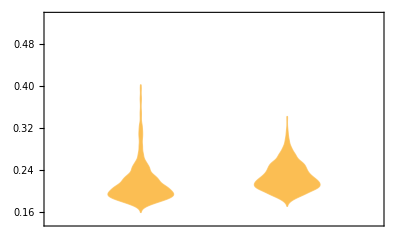

```mathematica
DistributionChart[{Transpose[controlXY][[10]],Transpose[controlXY][[11]]}]
```

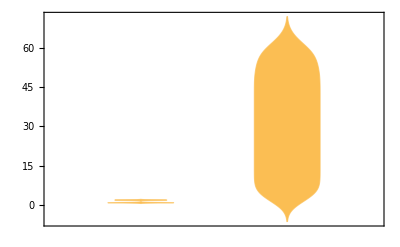

```mathematica
DistributionChart[{Transpose[controlXY][[24]],Transpose[controlXY][[25]]}]
```

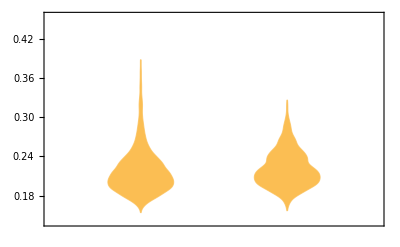

```mathematica
DistributionChart[{Transpose[tsaXY][[10]],Transpose[tsaXY][[11]]}]
```

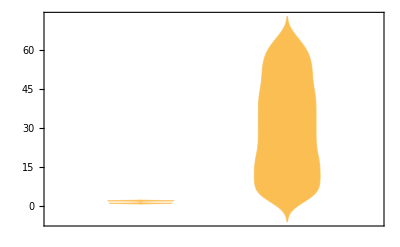

```mathematica
DistributionChart[{Transpose[tsaXY][[24]],Transpose[tsaXY][[25]]}]
```

```mathematica
Map[Mean,{Transpose[controlXY][[10]],Transpose[controlXY][[11]],Transpose[controlXY][[24]],Transpose[controlXY][[25]],Transpose[tsaXY][[10]],Transpose[tsaXY][[11]],Transpose[tsaXY][[24]],Transpose[tsaXY][[25]]}]
```

{0.216144,0.227045,271/188,76787/2444,0.218899,0.221186,4612/3049,94070/3049}

```mathematica
DistributionChart[{Transpose[controlXY][[10]],Transpose[controlXY][[11]]}]
```

-Graphics-

```mathematica
DistributionChart[{Transpose[controlXY][[24]],Transpose[controlXY][[25]]}]
```

-Graphics-

```mathematica
DistributionChart[{Transpose[tsaXY][[10]],Transpose[tsaXY][[11]]}]
```

-Graphics-

```mathematica
DistributionChart[{Transpose[tsaXY][[24]],Transpose[tsaXY][[25]]}]
```

-Graphics-

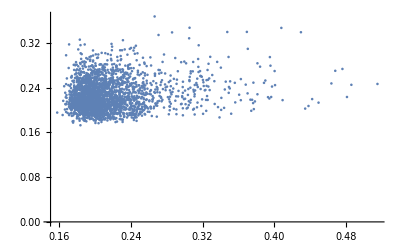

```mathematica
ListPlot[Transpose[{Transpose[controlXY][[10]],Transpose[controlXY][[11]]}],PlotRange->All]
```

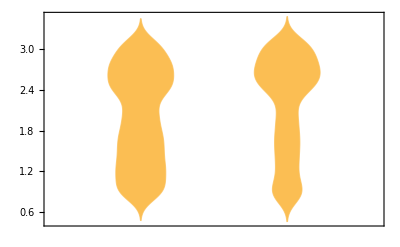

```mathematica
DistributionChart[Abs[{Transpose[controlXY][[12]],Transpose[controlXY][[31]]}]]
```

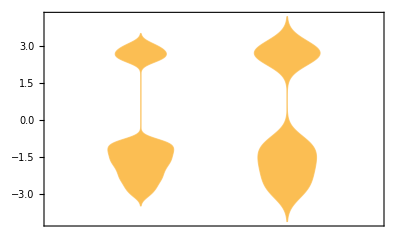

```mathematica
DistributionChart[{Transpose[controlXY][[12]],Transpose[controlXY][[31]]}]
```

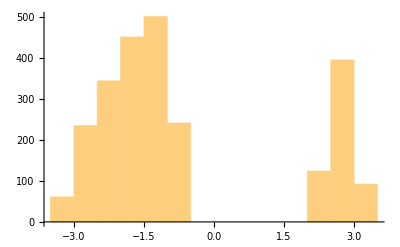

```mathematica
Histogram[Transpose[controlXY][[12]]]
```

```mathematica
anglecorrect[anglist_]:=Map[Which[Abs[#]<=Pi/2,#,#>Pi/2,Pi-#,#<-Pi/2,Pi+#]&,anglist]*180/Pi
```

```mathematica
absanglecorrect[anglist_]:=Abs[Map[Which[Abs[#]<=Pi/2,#,#>Pi/2,Pi-#,#<-Pi/2,Pi+#]&,anglist]*180/Pi]
```

```mathematica
[Abs[{Join[Pi-Abs[Transpose[controlXY][[12]]],Abs[Transpose[controlXY][[12]]]],Join[Abs[Transpose[controlXY][[26]]],Pi-Abs[Transpose[controlXY][[26]]]]}]]
```

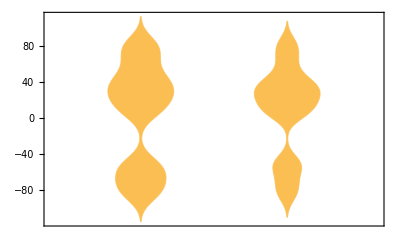

```mathematica
DistributionChart[{anglecorrect[Transpose[controlXY][[12]]],anglecorrect[Transpose[controlXY][[31]]]}]
```

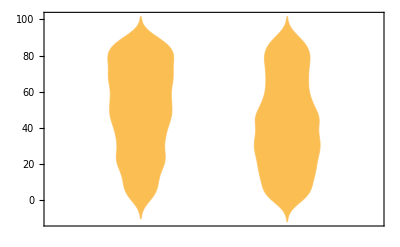

```mathematica
DistributionChart[{absanglecorrect[Transpose[controlXY][[12]]],absanglecorrect[Transpose[controlXY][[31]]]}]
```

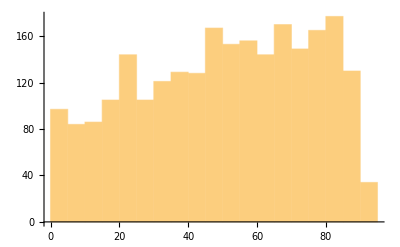

```mathematica
Histogram[absanglecorrect[Transpose[controlXY][[12]]]]
```

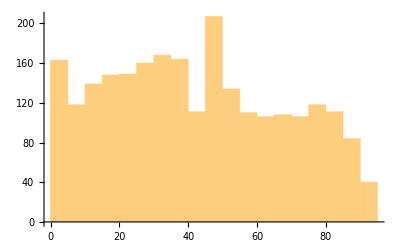

```mathematica
Histogram[absanglecorrect[Transpose[controlXY][[31]]]]
```

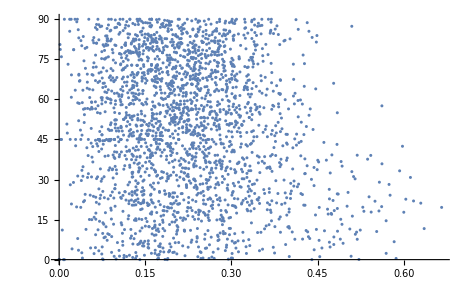

```mathematica
ListPlot[Transpose[{Transpose[controlXY][[13]],absanglecorrect[Transpose[controlXY][[12]]]}],PlotRange->All]
```

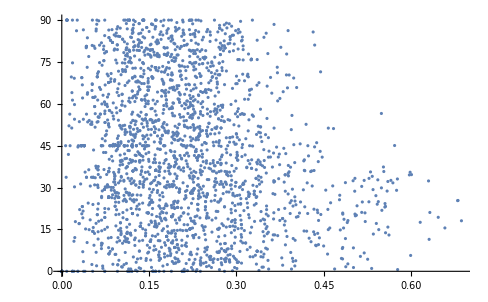

```mathematica
ListPlot[Transpose[{Transpose[controlXY][[32]],absanglecorrect[Transpose[controlXY][[31]]]}],PlotRange->All]
```

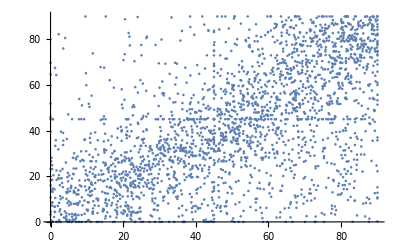

```mathematica
ListPlot[Transpose[{absanglecorrect[Transpose[controlXY][[12]]],absanglecorrect[Transpose[controlXY][[31]]]}],PlotRange->All]
```

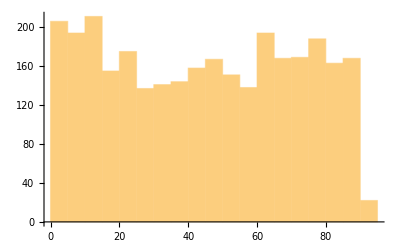

```mathematica
Histogram[absanglecorrect[Transpose[tsaXY][[12]]]]
```

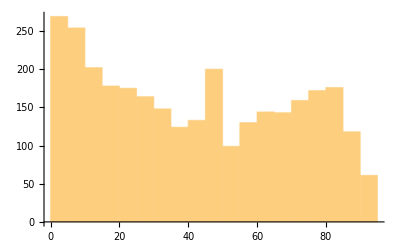

```mathematica
Histogram[absanglecorrect[Transpose[tsaXY][[31]]]]
```

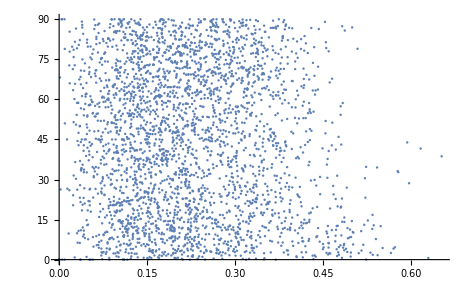

```mathematica
ListPlot[Transpose[{Transpose[tsaXY][[13]],absanglecorrect[Transpose[tsaXY][[12]]]}],PlotRange->All]
```

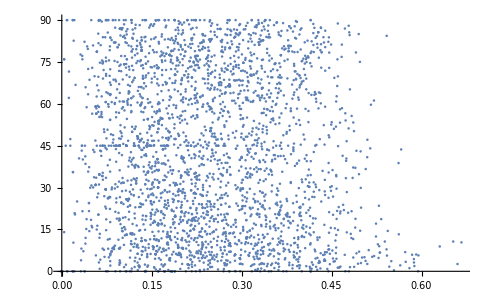

```mathematica
ListPlot[Transpose[{Transpose[tsaXY][[32]],absanglecorrect[Transpose[tsaXY][[31]]]}],PlotRange->All]
```

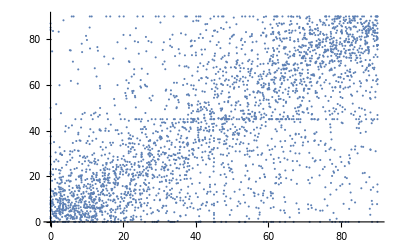

```mathematica
ListPlot[Transpose[{absanglecorrect[Transpose[tsaXY][[12]]],absanglecorrect[Transpose[tsaXY][[31]]]}],PlotRange->All]
```

```mathematica
Join[Transpose[{Abs[Transpose[controlXY][[12]]],Abs[Transpose[controlXY][[31]]]}],Transpose[{Pi-Abs[Transpose[controlXY][[12]]],Pi-Abs[Transpose[controlXY][[31]]]}]]
```

{{2.33917,2.33008},{2.37954,2.44448},{2.20857,2.36351},{2.19311,2.16403},{2.01912,2.14786},4878,{0.780054,2.11122},{0.785398,0.785398},{0.850504,0.785398},{1.31877,0.566015},{1.72115,0.36754}}
 |  |  |  |

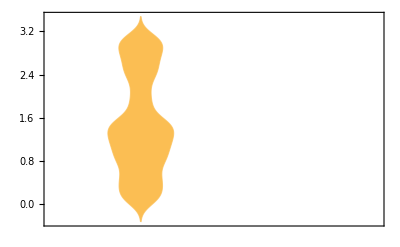

```mathematica
DistributionChart[Abs[{Join[Abs[Transpose[tsaXY][[12]]]-Pi/2,Abs[Transpose[tsaXY][[12]]]],Join[Abs[Transpose[tsaXY][[26]]],Abs[Transpose[tsaXY][[26]]]-Pi/2]}]]
```

```mathematica
Abs[Abs[{Join[Pi-Transpose[tsaXY][[12]],Transpose[tsaXY][[12]]],Join[Transpose[tsaXY][[26]],Pi-Transpose[tsaXY][[26]]]}]]
```

{{4.89953,4.86771,4.9397,4.90865,4.57403,4.28675,0.627763,4.73155,5.49288,4.67262,6078,2.47987,2.52834,2.29593,2.4925,2.37035,2.20782,3.04377,3.03408,2.77877,2.65287},{1}}
 |  |  |  |

```mathematica
tailcontrol1=Select[controlXY,#[[15]]=="True"&];
```

```mathematica
tailcontrol2=Select[controlXY,#[[34]]=="True"&];
```

```mathematica
tailtsa1=Select[tsaXY,#[[15]]=="True"&];
```

```mathematica
tailtsa2=Select[tsaXY,#[[34]]=="True"&];
```

```mathematica
taildirection[list_]:=Map[Which[#=="right",+1,#=="left",-1]&,list]
```

```mathematica
taildirection[Transpose[tailcontrol][[16]]]
```

{1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,1,1,-1,1,-1,-1,1,1,1,1,-1,1,1,1,1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,1,1,1,1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

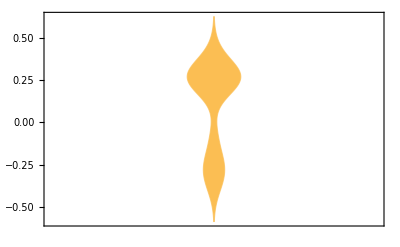

```mathematica
DistributionChart[{Transpose[tailcontrol1][[17]]*taildirection[Transpose[tailcontrol1][[16]]]}]
```

```mathematica
DistributionChart[{Transpose[tailcontrol2][[36]]*taildirection[Transpose[tailcontrol2][[35]]]}]
```

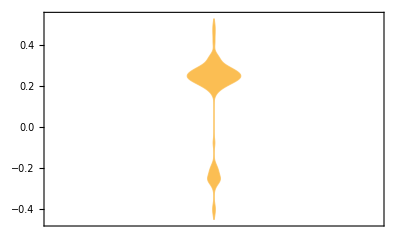

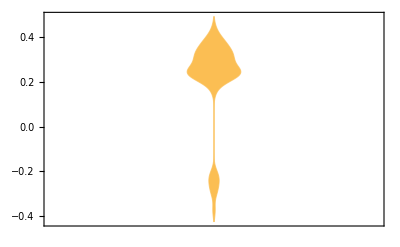

```mathematica
DistributionChart[{Transpose[tailtsa1][[36]]*taildirection[Transpose[tailtsa1][[35]]]}]
```

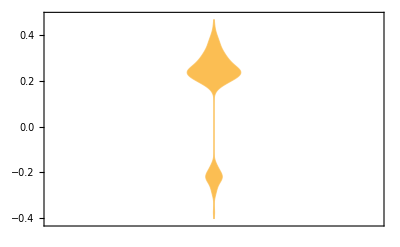

```mathematica
DistributionChart[{Transpose[tailtsa2][[36]]*taildirection[Transpose[tailtsa2][[35]]]}]
```

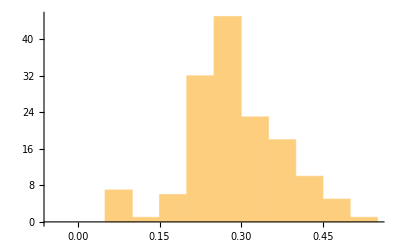

```mathematica
Histogram[Transpose[controlXY][[17]]]
```

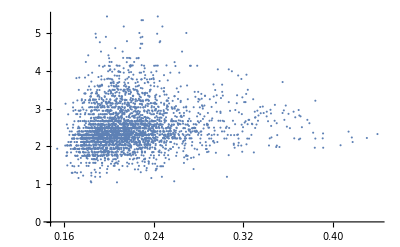

```mathematica
ListPlot[Transpose[{Transpose[tsaXY][[10]],Transpose[tsaXY][[18]]}],PlotRange->All]
```

```mathematica
ListPlot[Transpose[{Transpose[controlXY][[10]],Transpose[controlXY][[11]]}],PlotRange->All]
```

-Graphics-

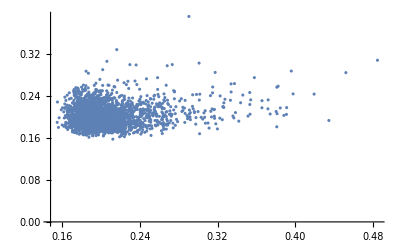

```mathematica
ListPlot[Transpose[{Transpose[controlXY][[29]],Transpose[controlXY][[30]]}],PlotRange->All]
```

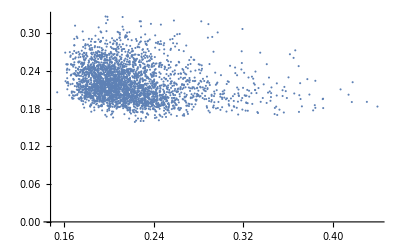

```mathematica
ListPlot[Transpose[{Transpose[tsaXY][[10]],Transpose[tsaXY][[11]]}],PlotRange->All]
```

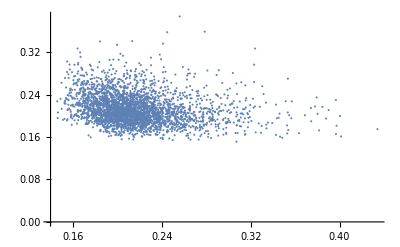

```mathematica
ListPlot[Transpose[{Transpose[tsaXY][[29]],Transpose[tsaXY][[30]]}],PlotRange->All]
```

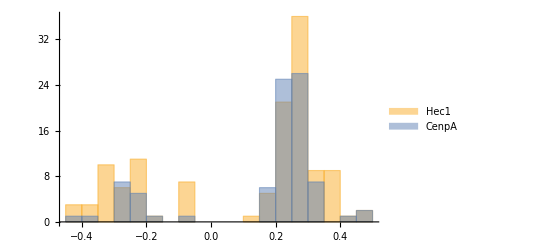

```mathematica
Histogram[{Transpose[tailcontrol1][[17]]*taildirection[Transpose[tailcontrol1][[16]]],Transpose[tailcontrol2][[36]]*taildirection[Transpose[tailcontrol2][[35]]]},20,PlotRange->All,ChartLegends->{Hec1, CenpA}]
```

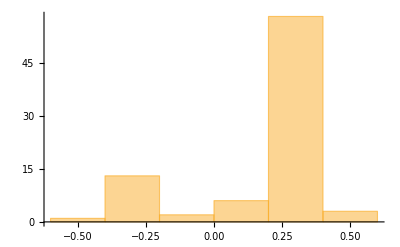

```mathematica
Histogram[{Transpose[tailcontrol2][[36]]*taildirection[Transpose[tailcontrol2][[35]]]},PlotRange->All]
```

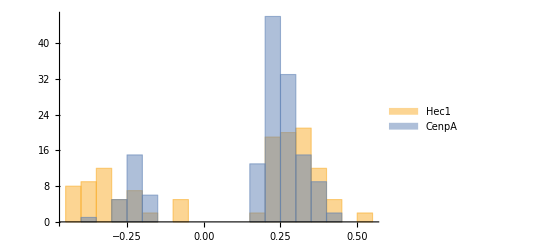

```mathematica
Histogram[{Transpose[tailtsa1][[17]]*taildirection[Transpose[tailtsa1][[16]]],Transpose[tailtsa2][[36]]*taildirection[Transpose[tailtsa2][[35]]]},20,PlotRange->All,ChartLegends->{Hec1, CenpA}]
```

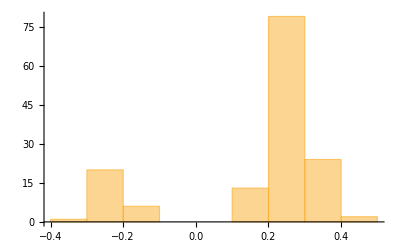

```mathematica
Histogram[{Transpose[tailtsa2][[36]]*taildirection[Transpose[tailtsa2][[35]]]},PlotRange->All]
```

```mathematica
ktXYdatatest44export2=Table[Table[Table[Table[Table[If[StringQ[ktdatapaths[[n]][[m]][[l]][[j]][[i]]]&&StringQ[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]]&&Length[Select[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]],!lis25[#]&]]==0&&Length[Select[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]],!lis25[#]&]]==0,Table[If[havedata[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]]]&&Length[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]]]>=t&&havedata[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]]],Join[{n,m,l,j,i,t,"/"},Join[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]],{"//"},{kkdata[[n]][[m]][[l]][[j]][[i]][[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]][[t]][[1]]]]},{ktdatapaths[[n]][[m]][[l]][[j]][[i]]}],{"////",n,m,conjugate[l],j,i,t,"/"},Join[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]],{"//"},{kkdata[[n]][[m]][[conjugate[l]]][[j]][[i]][[Import[ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]][[t]][[1]]]]},{ktdatapaths[[n]][[m]][[conjugate[l]]][[j]][[i]]}]]],{t,Length[Import[ktdatapaths[[n]][[m]][[l]][[j]][[i]]]]}]],{i,Length[ktdatapaths[[n]][[m]][[l]][[j]]]}],{j,Length[ktdatapaths[[n]][[m]][[l]]]}],{l,Length[ktdatapaths[[n]][[m]]]}],{m,Length[ktdatapaths[[n]]]}],{n,Length[ktdatapaths]}]
```

Part::partw: Part 2 of {D:\combine0802\control\new(2)(1) -new\ch1\13.-7\Path from Track_7 to Track_7.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\13.-7_(+-1)_NewResult_0908XYnew.csv} does not exist.

Part::partw: Part 2 of {D:\combine0802\control\new(3)\ch1\10.-2\Path from Track_2 to Track_2.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\10.-2_(+-1)_NewResult_0908XYnew.csv} does not exist.

Part::partw: Part 2 of {D:\combine0802\tsa\new (3)\ch2\15.-2\Path from Track_15 to Track_15.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 9}, Day]0908resultXYnew\newMethod\15.-2_(+-1)_NewResult_0908XYnew.csv} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{1},{1}}
 |  |  |  |

```mathematica
ktXYflatten44export2={Flatten[ktXYdatatest44export2[[1]],4],Flatten[ktXYdatatest44export2[[2]],4]}
```

{{Null,5014,Null},{Null,6259,{2,9,2,5,2,61,/,60,True,23,-2.65287,0.0879415,0.912059,False,,0.046*"",//,2.6054,D:\combine0802\tsa\newfolder(2,1) - new (2)\ch1\4.-6\Path from Track_6 to Track_6.tifcroppedimages\(+-1)\newXYnew\DateObject[{2023, 9, 10}, Day]0908resultXYnew\newMethod\4.-6_(+-1)_NewResult_0908XYnew.csv}}}
 |  |  |  |

```mathematica
Export["controlXYnew0907.csv",Select[ktXYflatten44export2[[1]],ListQ[#]&&#[[3]]==1&]]
```

controlXYnew0907.csv

```mathematica
Export["TSAXYnew0907.csv",Select[ktXYflatten44export2[[2]],ListQ[#]&&#[[3]]==1&]]
```

TSAXYnew0907.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["TSAXYnew0907.csv"]]]
```

```mathematica
controlXY0911=Import["controlXYnew0907.csv"];
```

```mathematica
tsaXY0911=Import["TSAXYnew0907.csv"];
```

```mathematica
tailcontrol1new=Select[controlXY0911,#[[15]]=="True"&];
```

```mathematica
tailcontrol2new=Select[controlXY0911,#[[34]]=="True"&];
```

```mathematica
tailtsa1new=Select[tsaXY0911,#[[15]]=="True"&];
```

```mathematica
tailtsa2new=Select[tsaXY0911,#[[34]]=="True"&];
```

```mathematica
taildirection[list_]:=Map[Which[#=="right",+1,#=="left",-1]&,list]
```

```mathematica
(*taildirection[Transpose[tailcontrol][[16]]]*)
```

Part::partw: Part 36 of {} does not exist.

Part::partw: Part 35 of {} does not exist.

Part::pkspec1: The expression Null cannot be used as a part specification.

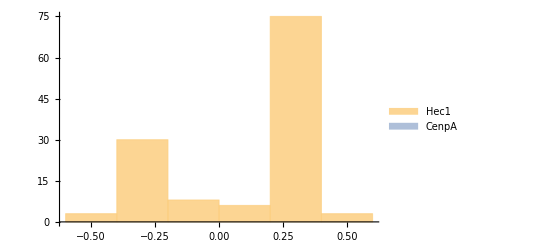

```mathematica
Histogram[{Transpose[tailcontrol1new][[17]]*taildirection[Transpose[tailcontrol1new][[16]]],Transpose[tailcontrol2new][[36]]*taildirection[Transpose[tailcontrol2new][[35]]]},PlotRange->All,ChartLegends->{Hec1, CenpA}]
```

Part::partw: Part 36 of {} does not exist.

Part::partw: Part 35 of {} does not exist.

Part::pkspec1: The expression Null cannot be used as a part specification.

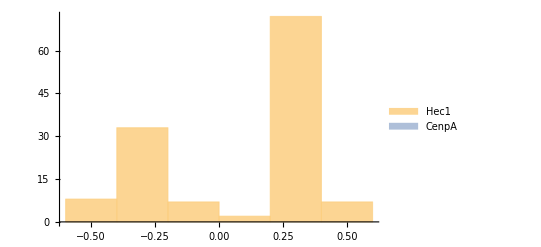

```mathematica
Histogram[{Transpose[tailtsa1new][[17]]*taildirection[Transpose[tailtsa1new][[16]]],Transpose[tailtsa2new][[36]]*taildirection[Transpose[tailtsa2new][[35]]]},PlotRange->All,ChartLegends->{Hec1, CenpA}]
```

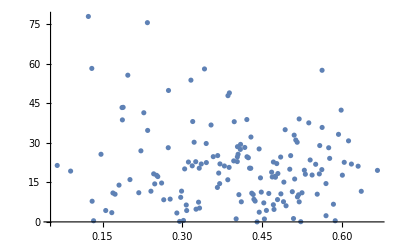

```mathematica
ListPlot[Transpose[{Transpose[tailcontrol1][[13]],absanglecorrect[Transpose[tailcontrol1][[12]]]}],PlotRange->All]
```

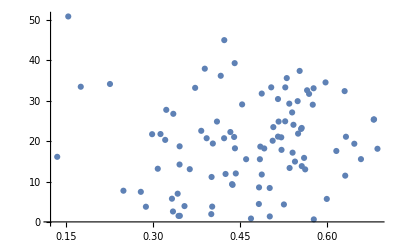

```mathematica
ListPlot[Transpose[{Transpose[tailcontrol2][[32]],absanglecorrect[Transpose[tailcontrol2][[31]]]}],PlotRange->All]
```

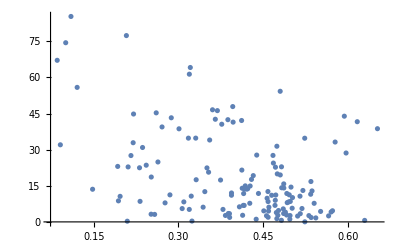

```mathematica
ListPlot[Transpose[{Transpose[tailtsa1][[13]],absanglecorrect[Transpose[tailtsa1][[12]]]}],PlotRange->All]
```

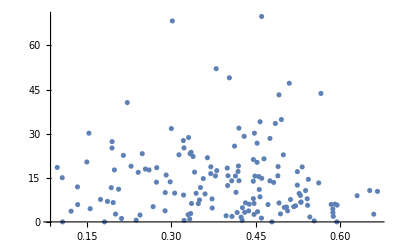

```mathematica
ListPlot[Transpose[{Transpose[tailtsa2][[32]],absanglecorrect[Transpose[tailtsa2][[31]]]}],PlotRange->All]
```

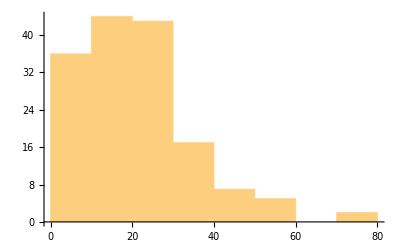

```mathematica
Histogram[absanglecorrect[Transpose[tailcontrol1][[12]]]]
```

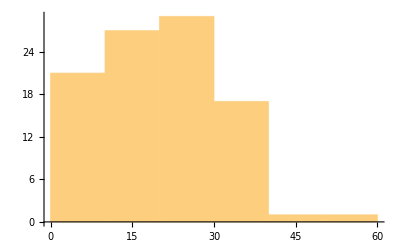

```mathematica
Histogram[absanglecorrect[Transpose[tailcontrol2][[31]]]]
```

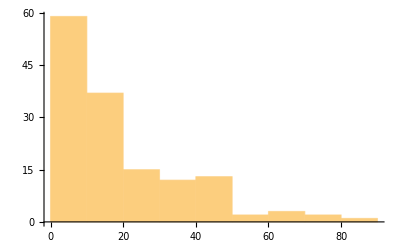

```mathematica
Histogram[absanglecorrect[Transpose[tailtsa1][[12]]]]
```

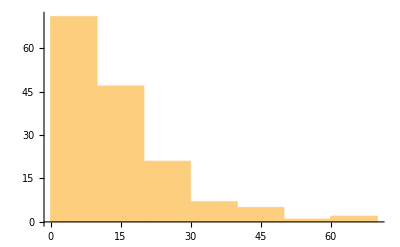

```mathematica
Histogram[absanglecorrect[Transpose[tailtsa2][[31]]]]
```

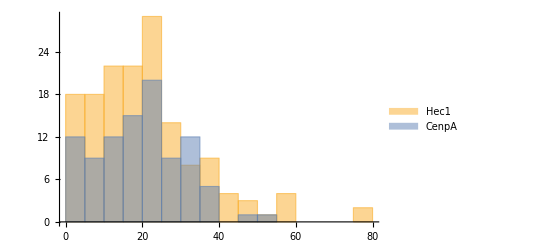

```mathematica
Histogram[{absanglecorrect[Transpose[tailcontrol1][[12]]],absanglecorrect[Transpose[tailcontrol2][[31]]]},20,PlotRange->All,ChartLegends->{Hec1, CenpA}]
```

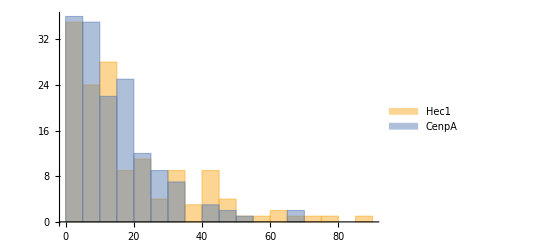

```mathematica
Histogram[{absanglecorrect[Transpose[tailtsa1][[12]]],absanglecorrect[Transpose[tailtsa2][[31]]]},20,PlotRange->All,ChartLegends->{Hec1, CenpA}]
```

```mathematica
Length[controlXY]
```

2444

```mathematica
Length[tsaXY]
```

3049

```mathematica
Length[tailcontrol1]
```

```mathematica
Length[tailcontrol2]
```

```mathematica
Length[tailtsa1]
```

```mathematica
Length[tailtsa2]
```